# R-sdSP learns the correct spike-timing in a navigational task with binary and delayed feedback.

```mathematica
ClearAll["Global`*"]
```

ClearAll::wrsym: Symbol k2 is Protected.

ClearAll::wrsym: Symbol Tmax is Protected.

ClearAll::wrsym: Symbol tNMDA is Protected.

General::stop: Further output of ClearAll :: wrsym will be suppressed during this calculation.

```mathematica
SetDirectory[NotebookDirectory[]]
```

/home/mathieu/Copy/dendritic_tree3/OnlineAMPANegW/ForPaper

Code

### Init

```mathematica
$HistoryLength=100;
```

### compilation Attributes

```mathematica
Const/: (a_Symbol = Const[b_]) :=
(a =b; SetAttributes[a,Protected]; b)
```

```mathematica
SetAttributes[InlComp,HoldAll];
InlComp[inls_,parms_,code_,decl_] :=
Block[ {curprot,Trans2Rule,r1,r2,rcode,a,cmp,t},

curprot := Block[ {t,a,s} ,
t = Names[$Context<>"*"];
a = Map[Attributes,t];
t=t[[ Map[First,Position[a,Protected,{2}]] ]];t= Map[ToExpression[#,StandardForm,Hold]&,t]
];

SetAttributes[Trans2Rule,HoldAll];
    Trans2Rule[sym_] := Block[ {t},
t = DownValues[sym];
If [Length[t] == 0,
{HoldPattern[sym] -> sym},
t]
];

SetAttributes[cmp,HoldAll];

r1  = Apply[Trans2Rule,curprot,{1}];
r2 = Map[Trans2Rule,Unevaluated@inls];
rcode = Hold[code] //. Flatten[{r1,r2}];
t=cmp[parms,rcode,decl] /. HoldPattern[rcode]-> rcode /. Hold[a___] -> a;
Compile@@t
]
```

```mathematica
GlobalRefs[f_CompiledFunction]:= Block[ {a,b},
Cases[
f[[4]], 
HoldPattern[Function[a_List, b___]] -> HoldForm[b],
∞
]
]
```

## set values

```mathematica
NN=150;
 
(* input dimension *)
Tmax = Const[500];  (* max. inputlength *)
step = 0.2; 
Tonl=Const[Tmax];(* τM in paper (for the elgibility trace low pass filter) *)
w = Table[1,{NN}]; (* no weight!!! *)
Urest = -1 ;(* resting potential *)
(*α : factor of reduction of s^ν and Subscript[E, i] over one time step *)
α=N[1-step/Tonl];
(*β : factor of reduction of Subscript[e, i] over one time step *)
β=N[step/Tonl];
γ=N[1/Tonl];
(*invE : threshold for s^ν *)
tmr = 10.0; (* decay time of the reset kernel *)
tmrini =N[ 10/tmr]; (* constant to update resets of spiking neurons *)
tmrsfac=N[1-step/tmr]; (* factor of reduction of the reset kernel over one time step *)
rewdelay = 0.;(*delay for a reward *)
FlucLen =0; (* to modulate the pattern length *)
λ=1; (* smoothing factor for the exponential moving average *)
tNMDA=50//Const;(*duration of a NMDA spike *)
stNMDA= IntegerPart[tNMDA/step]; (* number of steps for a NMDA spike *)
stNMDAReal=1.0*stNMDA;(* number of steps for a NMDA spike *)
UspikeNMDA=0.3;
mu=0.1;
pConnect=0.5;(* connectivity probability *)
β2=5.;
Umax=10.0//Const (*for the dendritic branches*);
UmaxSoma=2.0//Const (*for the soma until le first order approx is quite correct*);
sigma=1.4;
pOff=0.2;
nbNeuron=40;
τfracSp=4;
msNumber=-Log[$MachineEpsilon *100.];
```

Set::wrsym: Symbol Tmax is Protected.

Set::wrsym: Symbol Tonl is Protected.

Set::wrsym: Symbol tNMDA is Protected.

Set::wrsym: Symbol Umax is Protected.

Set::wrsym: Symbol UmaxSoma is Protected.

```mathematica
nStates=2;(* number of states to the left or the right of the tatget state*)
```

```mathematica
UrestSoma=-1.6;
```

```mathematica
cSpikeTime=Tonl/2;(* desired spike time *)
cSpikeTimeStep=cSpikeTime/step;(* desired spike time (number of step) *)
```

```mathematica
τfrac=0.5//Const (* fraction of time cte for the low pass filters *);
```

Set::wrsym: Symbol τfrac is Protected.

```mathematica
BoundSyn=100;
```

```mathematica
k2=Const[0.006737946999085467];
```

Set::wrsym: Symbol k2 is Protected.

```mathematica
LearnSpike=True;
```

```mathematica
aAMPA:=N[1./(2*nbNeuron)];
```

```mathematica
stepperlist=0;(* to keep the membrane potential in "stepper" *)
```

```mathematica
setStep[newStep_]:=(step=newStep;αg=N[1-step/Tonl];βg=N[step/Tonl];γg=N[1/Tonl];αl=N[1-step/tNMDA];βl=N[step/tNMDA];γl=N[1/tNMDA];tmrsfac=N[1-step/tmr];stNMDA= IntegerPart[tNMDA/step];stNMDAReal=1.0*stNMDA;);
```

```mathematica
setStep[step];
```

## Develop functions

### load packages

```mathematica
(* to write in the Messages windows *)
msg[expr_] := NotebookWrite[First@Notebooks["Messages"],
Cell[BoxData[MakeBoxes[expr,StandardForm]],"Output"]];
```

### define getFileName

```mathematica
getFileName[lstep_,trials_, opt_]:="./out/"<>"_eta"<>ToString[lstep//N]<>"_nbGames"<>ToString[trials]<>"_IL"<>ToString[NN]<>"_NbNeurons"<>ToString[nbNeuron]<>"_USpike"<>ToString[UspikeNMDA]<>"_nStates"<>ToString[nStates]<>"_SigmaW"<>ToString[σW]<>"_UrS"<>ToString[UrestSoma]<>"_aAMPA"<>ToString[aAMPA]<>"_"<>opt<>".out"
```

### define postsynaptic and reset kernel

```mathematica
myeps[] := Block[ {tm = 10.0,ts=1.5}, 
  (ⅇ^(-t/tm)-ⅇ^(-t/ts))/(tm-ts)]
```

```mathematica
myeta[]:= Block[ {tm = 10.0},
ⅇ^(-t/tm)/tm];
```

```mathematica
eps[t_] =myeps[];
SetAttributes[eps,Listable];
eta[t_] = 3myeta[];
SetAttributes[eta,Listable];
```

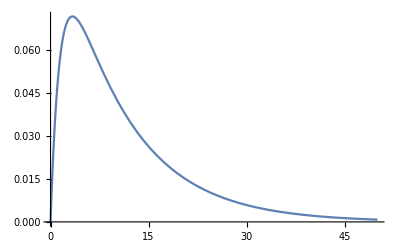

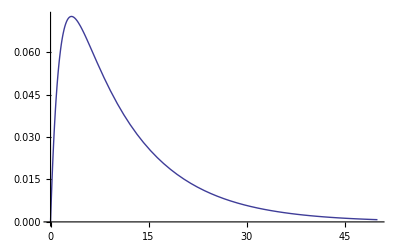

```mathematica
Plot[eps[t],{t,0,50}]
```

```mathematica
Integrate[eps[t],{t,0,∞}]
```

1.

### define stochastic intensity

```mathematica
(* escape noise for the dendrites *)
(*{ϕN,DϕN,DlϕN} = Block[ 
{k =100.(* firing at saturation *),β =5.0 (* Noise*),d =40000.0 (* shift factor*),dd,
f,df,dlf,u,kk,ββ ,a,b,c, cc},
f =  kk/(1+dd*Exp[-ββ*t]);
df =(kk*dd*ββ*Exp[-ββ*t])/(1+dd*Exp[-ββ*t])^2;
dlf = (ββ*dd)/(Exp[ββ*t]+dd);
{f,df,dlf} ={f,df,dlf}  /. {kk -> k,ββ ->  β,dd ->  d};
Map[ Function[ {t}, #]&, {a,b,c  +cc*t}]/. {a -> f, b-> df, c-> dlf,cc ->0.}
];*)
```

```mathematica
(* escape noise for the dendrites *)
{ϕN,DϕN,DlϕN} = Block[ 
{k =5.(* firing at saturation *),β =5.0 (* Noise*),d =1096.63(* shift factor*),dd,
f,df,dlf,u,kk,ββ ,a,b,c, cc},
f =  kk/(1.0+dd*t);
df =(kk*dd*ββ*t)/(1.0+dd*t)^2;
dlf = (ββ*dd)/(1./t+dd);
{f,df,dlf} ={f,df,dlf}  /. {kk -> k,ββ ->  β,dd ->  d};
Map[ Function[ {t}, #]&, {a,b,c  +cc*t}]/. {a -> f, b-> df, c-> dlf,cc ->0.}
];
```

```mathematica
(* escape noise for the soma *)
{ϕS,DϕS,DlϕS} = Block[ 
{k =k2,β =β2,
f,df,dlf,u,kk,ββ ,a,b,c, cc},
f =  kk ⅇ^(ββ *t);
df =kk ββ ⅇ^(ββ *t);
dlf = (*df/f*)ββ;
{f,df,dlf} ={f,df,dlf}  /. {kk -> k,ββ ->  β};
Map[ Function[ {t}, #]&, {a,b,c  +cc*t}]/. {a -> f, b-> df, c-> dlf,cc ->0.}
];
```

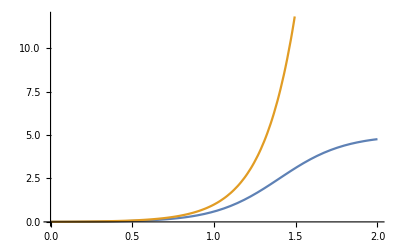

```mathematica
Plot[{ϕN[Exp[-β2 u]],ϕS[u]},{u,0,2}]
```

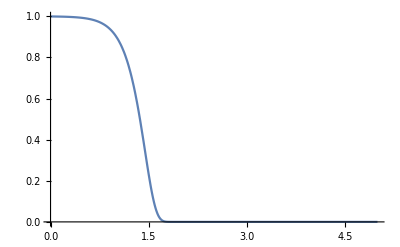

```mathematica
Plot[{step ϕS[u]/(ⅇ^(step ϕS[u])-1.)},{u,0,5},PlotRange->All]
```

```mathematica
step ϕS[u]/(ⅇ^(step ϕS[u])-1.)/.u->2
```

3.81504×10^-12

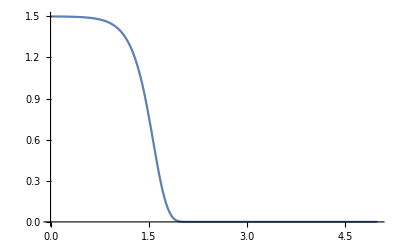

```mathematica
Plot[{Log[(1.-Exp[-ϕS[u]step])/(1.-Exp[- ϕS[u-0.3]step])]},{u,0,5},PlotRange->All]
```

```mathematica
1.-Exp[-ϕS[2.]step]
```

1.

```mathematica
Log[(1.-Exp[-ϕS[u]step])/(1.-Exp[- ϕS[u-0.3]step])]/.u->2.0
```

0.0013302

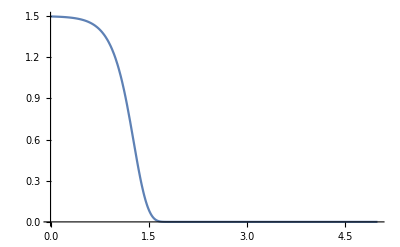

```mathematica
Plot[{Log[(1.-Exp[-ϕS[u+0.3]step])/(1.-Exp[- ϕS[u]step])]},{u,0,5},PlotRange->All]
```

```mathematica
Log[(1.-Exp[-ϕS[u+0.3]step])/(1.-Exp[- ϕS[u]step])]/.u->2.3
```

0.

### input: spikepattern X, corresponding synaptic potential epsps

```mathematica
Xin[]:=Block[{num=3,n,Xi},
    Xi:=(n=RandomInteger[PoissonDistribution[num]];
Sort[Table[RandomReal[] Tmax,{n}]]);
Table[Xi,{NN}]
];
```

```mathematica
Xin[]:=Block[{num=6,n,Xi},
    Xi:=(n=RandomInteger[PoissonDistribution[num]];
Select[Sort[Table[RandomReal[] 1000,{n}]],#≤Tonl&]);
Table[Xi,{NN}]
];
```

```mathematica
Inp[t_,X_,func_] :=
 (* add up the various spikes defined by <func> *)
Apply[Plus,
 func[
(* delete the negative times *)
 DeleteCases [t-X, a_/; a <0 ,{-1}]] ,
{1}(* only at the first level*) ];
```

```mathematica
Itimes = Table[ i step, {i,0,Floor[Tmax/step]}];
```

```mathematica
epsps[X_] :=Map[Inp[#,X,eps]&,Itimes]; (* Lists of synaptic potentials into each neuron for each (discretized) time *)
```

```mathematica
X = Xin[];
```

### define mempots

```mathematica
(* to calculate the membrane potential in the dendritic branchs *)
mempots[w_,inp_] := Block[ {tmp,us},
us=w.Transpose[inp]+Urest;
(*us= us* UnitStep[Umax-us]+Umax*UnitStep[us-Umax];*)(*saturation of the membrane potential at Umax *)
us
];
```

### define spikegenNMDA

```mathematica
(* spike or not with escape noise *)
spikegenNMDA[us_]:=
Block[{usf=Flatten[us],spikesi,t},
(*spikesi=Sign[step * ϕN[usf]-RandomReal[{0,1},Length[usf]]];*)
spikesi=Sign[1.-Exp[-step * ϕN[usf]]-RandomReal[{0,1},Length[usf]]];
If[Max[spikesi]≠1,{0},Flatten[Position[spikesi,1]]]
];
```

```mathematica
(* spike or not with escape noise *)
spikegenNMDA[us_,refPeriod_]:=
Block[{usf=Flatten[us],spikesi,t},
spikesi=Sign[step * ϕN[usf]*refPeriod-RandomReal[{0,1},Length[usf]]];If[Max[spikesi]≠1,{0},Flatten[Position[spikesi,1]]]
];
```

### define incrBuff

```mathematica
(* spike or not with escape noise *)
incrBuff[lindBuff_]:=
Block[{ind},
ind = Mod[lindBuff+1,stNMDA+1];
If[ind==0,1,ind]
];
```

### define myUnitStep

```mathematica
(Min[(tNMDA/(tNMDA+step)),Tonl/(Tonl+step)]+0.00001)/1000
```

0.000996026

```mathematica
myUnitStep[numb_]:=Block[{},
0.5*(Sign[(numb)+0.00099602593625498]+1.0)
];
```

### define ToFloat

```mathematica
ToFloat[numb_]:=Block[{numFl},
numFl=(numb*1.0);
numFl
];
```

### define SomaSat

```mathematica
SomaSat[u_]:=myUnitStep[UmaxSoma-u]u+myUnitStep[u-UmaxSoma]UmaxSoma;
```

### define stepper

```mathematica
stepper =
InlComp[
{mempots,spikegenNMDA,incrBuff,myUnitStep,ϕN,ϕS,k2,DϕN,DlϕN,DϕS,DlϕS,Tonl,step,stNMDA,tNMDA,β2,tmrsfac,αg,βg,γg,αl,βl,γl,UmaxSoma,τfrac,Urest,msNumber,UmaxSoma,SomaSat},
{{myinps,_Real,2},   (* input potentials *)
{myw,_Real,2},(* weights for the "dendritic neurons" and AMPA synapses for the first component*)
{resets,_Integer,1}, (* the NMDA spike response *)
{reset,_Real}, (* the reset kernel for the soma *)
{ETr,_Real,2}, (* the eligibility trace *)
{resets2,_Integer,1}, (* the NMDA spike response *)
{MemNMDASp,_Real,2}, (* memory of the synamtic state during the last NMDA spike *)
{BuffSyn,_Real,2} (* the no spiking part of Pfister ET over 50ms *)
},
Block[ {uSoma (*membrane potential at the soma *),ud, ntUpd,Updinc,thisinp,spikesNMDA,SpikeSoma,us,nw,i,len,istepperlist,mask,nmyresets,nmyreset,nBufUpd ,dendStructSpUpd,inRefPer,nUspikeNMDA,κ,ntAttIntSpikeNMDA,EligSoma,ntAttIntNMDA,intRefdendStruct,myET,indBuff=0,NMDASpikeCounts,θMultSpike=(1.15),nmBuffSyn,argFI,dendStruct,nmyinps,naAMPA,nτfracSp,nUrestSoma,ntmrini,FRS,nnStates},

(*local compy to change of context only at the begining*)
ntmrini=tmrini;
nUrestSoma=UrestSoma;
nmyinps=myinps;
mask = Mask;
nUspikeNMDA=UspikeNMDA;
nnStates=nStates;
κ=N[k2*(Exp[β2*nUspikeNMDA]-1.)];
len = Length[myinps];
istepperlist = stepperlist;
myET=(*0.0**)ETr;
nw = myw;
naAMPA=aAMPA;
nτfracSp=τfracSp;
nmyresets =(*0**)resets (*Table[0,{Length@nw}]*);
NMDASpikeCounts=resets2 ;
intRefdendStruct= nmyresets*0-stNMDA;
inRefPer=Table[0.,{Length@nw}];
dendStruct=Table[{1.},{Length@nw}];
NMDASpikeCounts=resets;
dendStructSpUpd= nUspikeNMDA*β2+inRefPer;
EligSoma=inRefPer;
nmyreset=(*0.**)reset;
Updinc=0.0*nw;
ntUpd=Updinc;
ntAttIntSpikeNMDA=(*0.0**)MemNMDASp(*Updinc*);(* memory of the state of the synapses when a NMDA spike occurs*)
(*represent the 50ms low pass filter of the no spiking part of Pfister ET*)
(*nBufUpd = BuffSyn*)(* Table[ntUpd,{stNMDA}]*);(* buffer for e^iv *)
ntAttIntNMDA=(*0.0**)BuffSyn; 
uSoma=0.;
EligSoma=inRefPer;
argFI=dendStruct;
FRS=0.;

For[i=1, i≤len,i++,
(*indBuff=incrBuff[indBuff];*)
nmyresets = nmyresets+1; (* refractoriness period *)
NMDASpikeCounts = NMDASpikeCounts+1; (* refractoriness period *)
inRefPer=0.5(Sign[nmyresets-0.1] +1.) ;(* determine the sign of the  attenuation integral *)

thisinp ={nmyinps[[i]]};   (* vector of inputs as a matrix *)
ud= mempots[nw,thisinp] ; (* calculate the membrane potential in the dendritic branchs ("line vector") *)
argFI=Exp[-β2*ud];
spikesNMDA= spikegenNMDA[argFI(*,inRefPer*)]; (* calculate the NMDA spikes *)
uSoma=nUspikeNMDA*Total[1.-inRefPer]-nmyreset+nUrestSoma+naAMPA*Total[Flatten@ud-Urest];
nmyreset = nmyreset  tmrsfac;
FRS=step * ϕS[SomaSat[uSoma]];
SpikeSoma=Sign[1.-Exp[-FRS]-RandomReal[{0,1}]];
(* somatic spike *)
If[SpikeSoma==1,
EligSoma=(*dendStructSpUpd*)Log[(1.-Exp[-FRS ⅇ^(nUspikeNMDA β2  inRefPer)])/(1.-Exp[-FRS ⅇ^(-nUspikeNMDA β2 (1.-inRefPer))])];
Updinc=(naAMPA* DlϕS[uSoma*dendStruct]FRS/(ⅇ^FRS-1.)).thisinp;
nmyreset+=ntmrini;
Sow[ i];,

EligSoma=-(step*κ)*Exp[β2*SomaSat[(uSoma-nUspikeNMDA)+nUspikeNMDA*inRefPer]];
Updinc=(-naAMPA*step*DϕS[SomaSat@uSoma*dendStruct]).thisinp;
];

ntUpd =Updinc+0.5 ntAttIntNMDA*EligSoma*inRefPer+0.5 ntAttIntSpikeNMDA*EligSoma*(1.0-inRefPer)(**(0.5(Sign[NMDASpikeCounts-0.1] +1.) )*);(*temrm without attenuation *)

(* calc of the eligibilite trace *)
Updinc =(step*DϕN[argFI]).thisinp;


(* NMDA spikes *)
If [spikesNMDA ≠ {0} ,(
NMDASpikeCounts[[spikesNMDA ]]=nmyresets[[spikesNMDA ]] ;
nmyresets[[spikesNMDA ]] = intRefdendStruct[[spikesNMDA ]];
Sow[ i,spikesNMDA];
us = argFI[[spikesNMDA]];
Updinc[[spikesNMDA]]=0.0*Updinc[[spikesNMDA]];
ntAttIntNMDA[[spikesNMDA]]=Updinc[[spikesNMDA]];
ntAttIntSpikeNMDA[[spikesNMDA]]=( DlϕN[us]).thisinp;

)];

(*myET=ntUpd+myET;*)
myET=ntUpd+(1.0-step/(τfrac(**nnStates *)Tonl))myET;

If[(istepperlist==1 ),
Sow[{uSoma,ud,nUspikeNMDA*Total[1.-inRefPer],naAMPA*Total[Flatten@ud-Urest]},"ReturnValue"];
];

(*ntAttIntNMDA=ntAttIntNMDA-nBufUpd[[indBuff]];
nBufUpd[[indBuff]]=Updinc;
ntAttIntNMDA=ntAttIntNMDA+Updinc;*)
ntAttIntNMDA=Updinc+(1.0-step/(0.5*tNMDA))*ntAttIntNMDA;
(*ntAttIntSpikeNMDA=(1.0-step/(0.5*tNMDA))*ntAttIntSpikeNMDA;*)
];
Sow[{uSoma,ud,0.0,0.0},"ReturnValue"];
Sow[{nw,nmyresets,nmyreset,myET,NMDASpikeCounts,ntAttIntSpikeNMDA,ntAttIntNMDA},"ReturnValue"];
],
{{Mask,_Real,2},{UspikeNMDA,_Real},{UrestSoma,_Real},{aAMPA,_Real},{τfracSp,_Real},{stepperlist,_Integer},{Position[_, 1],_Integer,2}}
];
```

```mathematica
GlobalRefs[stepper]
```

{}

### define passEpisode

#### pass at the beginning (no resets, lags(=s^⋁), deriv(=E_i) yet)

```mathematica
passEpisode[w_, inps_] := passEpisode[inps,w,Table[0,{Length@w}],0.0,0.0*w,Table[0,{Length@w}],0.0*w,0.0*w];
```

#### pass later

```mathematica
passEpisode[inps_,w_,resets_,reset_,ET_,resets2_,memNMDASp_,memSyn_] := Block[ {resl,Y,Z},
{{resl,Y},Z}  =Reap[Reap[
Reap[stepper[inps, w,resets,reset,ET,resets2,memNMDASp,memSyn],"ReturnValue"][[2,1]] ,
 Range@First@Dimensions@w]];
{resl,({Y,Z} /. {{a__}} -> {a})}
];
```

#### nextpass later

```mathematica
nextpassEpisode[inps_,lresl_] := (
passEpisode[inps,Sequence@@lresl]);
```

#### nextpass at the beginning

```mathematica
nextpassEpisode[inps_,ww_ini (*to differentiate the 2 func nextpass *) ] :=  passEpisode[First@ww,inps];
(* only if the second argument (ww_) is of type ini  *)
```

### define Eval functs

```mathematica
stepperEval =
InlComp[
{mempots,spikegenNMDA,incrBuff,myUnitStep,ϕN,ϕS,k2,DϕN,DlϕN,DϕS,DlϕS,Tonl,step,stNMDA,tNMDA,β2,tmrsfac,αg,βg,γg,αl,βl,γl,UmaxSoma,τfrac,Urest,msNumber,UmaxSoma,SomaSat},
{{myinps,_Real,2},   (* input potentia.ls *)
{myw,_Real,2},(* weights for the "dendritic neurons" and AMPA synapses for the first component*)
{resets,_Integer,1}, (* the NMDA spike response *)
{reset,_Real}, (* the reset kernel for the soma *)
{ETr,_Real,2}, (* the eligibility trace *)
{resets2,_Integer,1}, (* the NMDA spike response *)
{MemNMDASp,_Real,2}, (* memory of the synamtic state during the last NMDA spike *)
{BuffSyn,_Real,2} (* the no spiking part of Pfister ET over 50ms *)
},
Block[ {uSoma (*membrane potential at the soma *),ud, ntUpd,Updinc,thisinp,spikesNMDA,SpikeSoma,us,nw,i,len,istepperlist,mask,nmyresets,nmyreset,nBufUpd ,dendStructSpUpd,inRefPer,nUspikeNMDA,κ,ntAttIntSpikeNMDA,EligSoma,ntAttIntNMDA,intRefdendStruct,myET,indBuff=0,NMDASpikeCounts,θMultSpike=(1.15),nmBuffSyn,argFI,dendStruct,nmyinps,naAMPA,nτfracSp,nUrestSoma,ntmrini,FRS,nnStates},

(*local compy to change of context only at the begining*)
ntmrini=tmrini;
nUrestSoma=UrestSoma;
nmyinps=myinps;
mask = Mask;
nUspikeNMDA=UspikeNMDA;
nnStates=nStates;
κ=N[k2*(Exp[β2*nUspikeNMDA]-1.)];
len = Length[myinps];
istepperlist = stepperlist;
myET=(*0.0**)ETr;
nw = myw;
naAMPA=aAMPA;
nτfracSp=τfracSp;
nmyresets =(*0**)resets (*Table[0,{Length@nw}]*);
NMDASpikeCounts=resets2 ;
intRefdendStruct= nmyresets*0-stNMDA;
inRefPer=Table[0.,{Length@nw}];
dendStruct=Table[{1.},{Length@nw}];
NMDASpikeCounts=resets;
dendStructSpUpd= nUspikeNMDA*β2+inRefPer;
EligSoma=inRefPer;
nmyreset=(*0.**)reset;
Updinc=0.0*nw;
ntUpd=Updinc;
ntAttIntSpikeNMDA=(*0.0**)MemNMDASp(*Updinc*);(* memory of the state of the synapses when a NMDA spike occurs*)
(*represent the 50ms low pass filter of the no spiking part of Pfister ET*)
(*nBufUpd = BuffSyn*)(* Table[ntUpd,{stNMDA}]*);(* buffer for e^iv *)
ntAttIntNMDA=(*0.0**)BuffSyn; 
uSoma=0.;
EligSoma=inRefPer;
argFI=dendStruct;
FRS=0.;

For[i=1, i≤len,i++,
(*indBuff=incrBuff[indBuff];*)
nmyresets = nmyresets+1; (* refractoriness period *)
NMDASpikeCounts = NMDASpikeCounts+1; (* refractoriness period *)
inRefPer=0.5(Sign[nmyresets-0.1] +1.) ;(* determine the sign of the  attenuation integral *)

thisinp ={nmyinps[[i]]};   (* vector of inputs as a matrix *)
ud= mempots[nw,thisinp] ; (* calculate the membrane potential in the dendritic branchs ("line vector") *)
argFI=Exp[-β2*ud];
spikesNMDA= spikegenNMDA[argFI(*,inRefPer*)]; (* calculate the NMDA spikes *)
uSoma=nUspikeNMDA*Total[1.-inRefPer]-nmyreset+nUrestSoma+naAMPA*Total[Flatten@ud-Urest];
nmyreset = nmyreset  tmrsfac;
FRS=step * ϕS[SomaSat[uSoma]];
SpikeSoma=Sign[1.-Exp[-FRS]-RandomReal[{0,1}]];
(* somatic spike *)
If[SpikeSoma==1,
nmyreset+=ntmrini;
Sow[ i];
];

(* NMDA spikes *)
If [spikesNMDA ≠ {0} ,(
NMDASpikeCounts[[spikesNMDA ]]=nmyresets[[spikesNMDA ]] ;
nmyresets[[spikesNMDA ]] = intRefdendStruct[[spikesNMDA ]];
Sow[ i,spikesNMDA];
)];

If[(istepperlist==1 ),
Sow[{uSoma,Flatten@ud,nUspikeNMDA*Total[1.-inRefPer],naAMPA*Total[Flatten@ud-Urest]},"ReturnValue"];
];

];
Sow[{uSoma,ud,0.0,0.0},"ReturnValue"];
Sow[{nw,nmyresets,nmyreset,myET,NMDASpikeCounts,ntAttIntSpikeNMDA,ntAttIntNMDA},"ReturnValue"];
],
{{Mask,_Real,2},{UspikeNMDA,_Real},{UrestSoma,_Real},{aAMPA,_Real},{τfracSp,_Real},{stepperlist,_Integer},{Position[_, 1],_Integer,2}}
];
```

#### pass at the beginning (no resets, lags(=s^⋁), deriv(=E_i) yet)

```mathematica
passEpisodeEval[w_, inps_] := passEpisodeEval[inps,w,Table[0,{Length@w}],0.0,0.0*w,Table[0,{Length@w}],0.0*w,0.0*w];
```

#### pass later

```mathematica
passEpisodeEval[inps_,w_,resets_,reset_,ET_,resets2_,memNMDASp_,memSyn_] := Block[ {resl,Y,Z},
{{resl,Y},Z}  =Reap[Reap[
Reap[stepperEval[inps, w,resets,reset,ET,resets2,memNMDASp,memSyn],"ReturnValue"][[2,1]] ,
 Range@First@Dimensions@w]];
{resl,({Y,Z} /. {{a__}} -> {a})}
];
```

#### nextpass later

```mathematica
nextpassEpisodeEval[inps_,lresl_] := (
passEpisodeEval[inps,Sequence@@lresl]);
```

#### nextpass at the beginning

```mathematica
nextpassEpisodeEval[inps_,ww_ini (*to differentiate the 2 func nextpass *) ] :=  passEpisodeEval[First@ww,inps];
(* only if the second argument (ww_) is of type ini  *)
```

### define iniws (initial weights and Mask)

```mathematica
iniws[w_,num_,keepratio_]:=Block[{tmp,Mask},tmp=Norm[w,1]/Length[w];tmp=Table[w,{num}]+RandomReal[NormalDistribution[0,tmp],{num,Length[w]}];Mask=RandomReal[{0,1},{num,Length[w]}];
Mask=UnitStep[Mask-(1-keepratio)] 1.;
{tmp Mask,Mask}
]
```

### define myiniws

```mathematica
myiniws[μw_,σw_,num_,keepratio_]:=Block[{tmp,Mask},tmp=Table[μw,{num},{NN}];If[σw≠0,tmp+=RandomReal[NormalDistribution[0,σw],{num,NN}]];
Mask=RandomReal[{0,1},{num,NN}];
Mask=UnitStep[Mask-(1-keepratio)] 1.;
{tmp Mask,Mask}
]
```

### Def. functions to create patterns

```mathematica
Patn:=2 nStates+1;
 
(* number of patterns *)
Pats=Table[Xin[],{Patn}];
```

```mathematica
FlucLen=0;
MakePats[]:=(Pats=Table[Xin[],{Patn}];PatLen=Table[1+Round[(Tonl+2 FlucLen (Tmax-Tonl) (RandomReal[]-0.5))/step],{Patn}];)
```

```mathematica
Patsepsps0[n_] := Take[epsps[Pats[[n]]],PatLen[[n]]];
Clear[Patsepsps]; 
Patsepsps[n_]:=Patsepsps[n]=Patsepsps0[n];
(* patters as potentials *)
```

```mathematica
(*InhibInp0[n_] :=Map[Total,RotateRight[Patsepsps[n],Round[τInhib/step]]];
Clear[InhibInp]; 
InhibInp[n_]:=InhibInp[n]=InhibInp0[n];*)
```

### define rewardFct

```mathematica
cSpikeTimeStep
```

1250.

```mathematica
rewardFct[d_]:=Exp[- d/cSpikeTimeStep]-1.;
```

```mathematica
SetAttributes[rewardFct,Listable];
```

```mathematica
rewardFct2[d_]:=(Exp[-(d*step)^2/250^2]-1);
```

```mathematica
SetAttributes[rewardFct2,Listable];
```

```mathematica
(*give the Mean of the Initial Weights s.t. 80% of the synapses are exitatory*)
getMeanInitWeights[σ_,pOff_] := √2*σ*InverseErf[1-2.*pOff];
```

```mathematica
pOff=0.2;
```

### λFilter

```mathematica
(*exp. moving average *)
 λFilter[incs_,λ_] := Block[ {fm},
fm[s_,inc_] := (1-λ)s + λ inc; 
FoldList[fm,0.5,incs]//Rest
];
```

```mathematica
(*exp. moving average *)
 λFilter[incs_,λ_,iniV_] := Block[ {fm},
fm[s_,inc_] := (1-λ)s + λ inc; 
FoldList[fm,iniV,incs]//Rest
];
```

### Calc new states fcts

```mathematica
StateToPatn[state_] :=state+nStates+1;
```

```mathematica
PatnToState[p_] :=p-nStates-1;
```

```mathematica
incrState[n_,incr_]:=Mod[n+incr+nStates,Patn]-nStates;
```

```mathematica
CalcNewStates[Z_,n_]:=Block[{increment},
If[Length@Z>0,
increment=(Min[Z]-Tonl/2)/(Tonl/2) (nStates);
increment=Sign[increment] Ceiling@Abs[increment];
incrState[n,increment],
n
]
];
```

### define RunGame

```mathematica
nbRunMax=1000;
```

```mathematica
RunGame[neur_,iniState_,lRate_]:=Block[{Z,Y,n,k,lastD,R,deltaW},
n=iniState;
lastD=neur;
For[k=1,k≤nbRunMax,k++,
{lastD,{Y,Z}}=nextpassEpisode[Patsepsps[StateToPatn@n],lastD];
lastD=Last@lastD;(*we don't care about membrane pot*)

n=CalcNewStates[step Z,n];

R=1. UnitStep[0.1-Abs[n]]-1.;

(*temp=o;*)
deltaW=lastD[[4]]* Mask;

lastD[[1]]=lastD[[1]]+ lRate *R*deltaW;(* weight update *)

If[n===0,n=k;Return[{lastD,n}]]
];
{lastD,nbRunMax}
];
```

### define learnNavig

```mathematica
rewdelay=0.;
learnNavig[wwin_,nbGames_,lstep_]:=Block[{last,ns,c,tGame,temp,t,punishCoeff,i},
last=ini[wwin];
For[i=1,i≤nbGames,i++,
ns=RandomInteger[{-nStates,nStates}];
{last,tGame}=RunGame[last,ns,lstep];

Sow[{tGame,Norm[(Last@last)[[1]]],ns},ensemble];
(*msg[Z];*)
];
First@last
];
```

### define learnNavigInFile

```mathematica
learnNavigInFile[nbGames_,lstep_,opt_]:=Block[{tmp,tmp2,res,wwin,tmpSeed},
tmpSeed=IntegerPart[AbsoluteTime[]];
SeedRandom[tmpSeed];
Print["seed="<>ToString@tmpSeed];
{wwin,Mask} = myiniws[0.,σW,nbNeuron,pConnect];
MakePats[];
Clear[Patsepsps];
Patsepsps[n_]:=Patsepsps[n]=Patsepsps0[n];
(* patters as binarypotentials *)

tmp=Reap[learnNavig[wwin,nbGames,lstep],ensemble];
res=trialDT[outDT[Transpose[tmp[[2,1]]][[1]](* time for a Game *)],
outDT[Transpose[tmp[[2,1]]][[3]](* ini states *)],
outDT[Transpose[tmp[[2,1]]][[2]](* |Δw| *)],
outDT[tmp[[1]](* w *)],
outDT[tmpSeed]];
PutAppend[res,(getFileName[lstep,nbGames, opt])];
];
```

### define ContlearnInFile

```mathematica
ContlearnInFile[nbGames_,nbGames2_,lstep_,opt_]:=Block[{tmp,tmp2,res,wwin,Seedtab,WTab,k,PerfTab,ZTab,StatesTab,ΔwTab,outFileName,outSeedtab},
outFileName=getFileName[lstep,nbGames+nbGames2, opt];

res=ReadList[getFileName[lstep,nbGames, opt]];

PerfTab=res/.trialDT[outDT[a_],_,_,_,_,_]->a;
ZTab=res/.trialDT[_,outDT[a_],_,_,_,_]->a;
StatesTab=res/.trialDT[_,_,outDT[a_],_,_,_]->a;
ΔwTab=res/.trialDT[_,_,_,outDT[a_],_,_]->a;
WTab=res/.trialDT[_,_,_,_,outDT[a_],_]->a;
Seedtab=res/.trialDT[_,_,_,_,_,outDT[a_]]->a;


For[(*k=1,k≤Length@WTab,k++*)k=Length@WTab,1≤k,k--,
SeedRandom[Seedtab[[k]]];
{wwin,Mask} = myiniws[0.,σW,nbNeuron,pConnect];
MakePats[];
Clear[Patsepsps];
Patsepsps[n_]:=Patsepsps[n]=Patsepsps0[n];

outSeedtab=If[FileExistsQ[outFileName],ReadList[outFileName]/.trialDT[_,_,_,_,_,outDT[a_]]->a,{}];
If[FreeQ[outSeedtab,Seedtab[[k]]],
Print@Timing[tmp2=Reap[learnNavig[WTab[[k]],nbGames2,lstep],ensemble];];
res=trialDT[outDT[Join[PerfTab[[k]],Transpose[tmp2[[2,1]]][[1]]](* Perf *)],
outDT[Join[ZTab[[k]],Transpose[tmp2[[2,1]]][[2]]](* Z *)],
outDT[Join[StatesTab[[k]],Transpose[tmp2[[2,1]]][[3]]](* states *)],
outDT[Join[ΔwTab[[k]],Transpose[tmp2[[2,1]]][[4]]](* |Δw| *)],
outDT[tmp2[[1]]],
outDT[Seedtab[[k]]]
];
PutAppend[res,outFileName];
];
];
];
```

### define EvalStopSp functs

```mathematica
stepperEvalStopSp =
InlComp[
{mempots,spikegenNMDA,incrBuff,myUnitStep,ϕN,ϕS,k2,DϕN,DlϕN,DϕS,DlϕS,Tonl,step,stNMDA,tNMDA,β2,tmrsfac,αg,βg,γg,αl,βl,γl,UmaxSoma,τfrac,Urest,msNumber,UmaxSoma,SomaSat},
{{myinps,_Real,2},   (* input potentia.ls *)
{myw,_Real,2},(* weights for the "dendritic neurons" and AMPA synapses for the first component*)
{resets,_Integer,1}, (* the NMDA spike response *)
{reset,_Real}, (* the reset kernel for the soma *)
{ETr,_Real,2}, (* the eligibility trace *)
{resets2,_Integer,1}, (* the NMDA spike response *)
{MemNMDASp,_Real,2}, (* memory of the synamtic state during the last NMDA spike *)
{BuffSyn,_Real,2} (* the no spiking part of Pfister ET over 50ms *)
},
Block[ {uSoma (*membrane potential at the soma *),ud, ntUpd,Updinc,thisinp,spikesNMDA,SpikeSoma,us,nw,i,len,istepperlist,mask,nmyresets,nmyreset,nBufUpd ,dendStructSpUpd,inRefPer,nUspikeNMDA,κ,ntAttIntSpikeNMDA,EligSoma,ntAttIntNMDA,intRefdendStruct,myET,indBuff=0,NMDASpikeCounts,θMultSpike=(1.15),nmBuffSyn,argFI,dendStruct,nmyinps,naAMPA,nτfracSp,nUrestSoma,ntmrini,FRS,nnStates,contloop},

(*local compy to change of context only at the begining*)
ntmrini=tmrini;
nUrestSoma=UrestSoma;
nmyinps=myinps;
mask = Mask;
nUspikeNMDA=UspikeNMDA;
nnStates=nStates;
κ=N[k2*(Exp[β2*nUspikeNMDA]-1.)];
len = Length[myinps];
istepperlist = stepperlist;
myET=(*0.0**)ETr;
nw = myw;
naAMPA=aAMPA;
nτfracSp=τfracSp;
nmyresets =(*0**)resets (*Table[0,{Length@nw}]*);
NMDASpikeCounts=resets2 ;
intRefdendStruct= nmyresets*0-stNMDA;
inRefPer=Table[0.,{Length@nw}];
dendStruct=Table[{1.},{Length@nw}];
NMDASpikeCounts=resets;
dendStructSpUpd= nUspikeNMDA*β2+inRefPer;
EligSoma=inRefPer;
nmyreset=(*0.**)reset;
Updinc=0.0*nw;
ntUpd=Updinc;
ntAttIntSpikeNMDA=(*0.0**)MemNMDASp(*Updinc*);(* memory of the state of the synapses when a NMDA spike occurs*)
(*represent the 50ms low pass filter of the no spiking part of Pfister ET*)
(*nBufUpd = BuffSyn*)(* Table[ntUpd,{stNMDA}]*);(* buffer for e^iv *)
ntAttIntNMDA=(*0.0**)BuffSyn; 
uSoma=0.;
EligSoma=inRefPer;
argFI=dendStruct;
FRS=0.;
contloop=True;
For[i=1, (i≤len)&&contloop,i++,
(*indBuff=incrBuff[indBuff];*)
nmyresets = nmyresets+1; (* refractoriness period *)
NMDASpikeCounts = NMDASpikeCounts+1; (* refractoriness period *)
inRefPer=0.5(Sign[nmyresets-0.1] +1.) ;(* determine the sign of the  attenuation integral *)

thisinp ={nmyinps[[i]]};   (* vector of inputs as a matrix *)
ud= mempots[nw,thisinp] ; (* calculate the membrane potential in the dendritic branchs ("line vector") *)
argFI=Exp[-β2*ud];
spikesNMDA= spikegenNMDA[argFI(*,inRefPer*)]; (* calculate the NMDA spikes *)
uSoma=nUspikeNMDA*Total[1.-inRefPer]-nmyreset+nUrestSoma+naAMPA*Total[Flatten@ud-Urest];
nmyreset = nmyreset  tmrsfac;
FRS=step * ϕS[SomaSat[uSoma]];
SpikeSoma=Sign[1.-Exp[-FRS]-RandomReal[{0,1}]];
(* somatic spike *)
If[SpikeSoma==1,
nmyreset+=ntmrini;
contloop=False;
Sow[ i];
];

(* NMDA spikes *)
If [spikesNMDA ≠ {0} ,(
NMDASpikeCounts[[spikesNMDA ]]=nmyresets[[spikesNMDA ]] ;
nmyresets[[spikesNMDA ]] = intRefdendStruct[[spikesNMDA ]];
Sow[ i,spikesNMDA];
)];

If[(istepperlist==1 ),
Sow[{uSoma,Flatten@ud,nUspikeNMDA*Total[1.-inRefPer],naAMPA*Total[Flatten@ud-Urest]},"ReturnValue"];
];

];
Sow[{uSoma,ud,0.0,0.0},"ReturnValue"];
Sow[{nw,nmyresets,nmyreset,myET,NMDASpikeCounts,ntAttIntSpikeNMDA,ntAttIntNMDA},"ReturnValue"];
],
{{Mask,_Real,2},{UspikeNMDA,_Real},{UrestSoma,_Real},{aAMPA,_Real},{τfracSp,_Real},{stepperlist,_Integer},{Position[_, 1],_Integer,2}}
];
```

#### pass at the beginning (no resets, lags(=s^⋁), deriv(=E_i) yet)

```mathematica
passEpisodeEvalStopSp[w_, inps_] := passEpisodeEvalStopSp[inps,w,Table[0,{Length@w}],0.0,0.0*w,Table[0,{Length@w}],0.0*w,0.0*w];
```

#### pass later

```mathematica
passEpisodeEvalStopSp[inps_,w_,resets_,reset_,ET_,resets2_,memNMDASp_,memSyn_] := Block[ {resl,Y,Z},
{{resl,Y},Z}  =Reap[Reap[
Reap[stepperEvalStopSp[inps, w,resets,reset,ET,resets2,memNMDASp,memSyn],"ReturnValue"][[2,1]] ,
 Range@First@Dimensions@w]];
{resl,({Y,Z} /. {{a__}} -> {a})}
];
```

#### nextpass later

```mathematica
nextpassEpisodeEvalStopSp[inps_,lresl_] := (
passEpisodeEvalStopSp[inps,Sequence@@lresl]);
```

#### nextpass at the beginning

```mathematica
nextpassEpisodeEvalStopSp[inps_,ww_ini (*to differentiate the 2 func nextpass *) ] :=  passEpisodeEvalStopSp[First@ww,inps];
(* only if the second argument (ww_) is of type ini  *)
```

## Plot functions

```mathematica
Needs["PlotLegends`"]
```

```mathematica
Needs["ErrorBarPlots`"]
```

### define PlotnTimeInFile

```mathematica
PlotnTimeInFile[trials_,lstep_,opt_]:=Block[{tmp,res},
res=ReadList[getFileName[lstep,trials, opt]]/.trialDT[outDT[a_],_,_,_,_]->a;
ListLinePlot[ λFilter[Mean@res,0.2/Patn,0],FrameLabel->{"trials","<Time>"},
PlotLabel->"η="<>ToString[lstep]<>"  nStates="<>ToString[nStates]<>"  Runs="<>ToString[Length@res],
Frame->True,PlotRange->All]
];
```

```mathematica
PlotPerfsInFile[trials_,lstep_,opt_]:=Block[{tmp,res},
res=ReadList[getFileName[lstep,trials, opt]]/.trialDT[outDT[a_],_,_,_,_]->a;
ListAnimate[Map[ListLinePlot[ λFilter[#,0.2/Patn,0],FrameLabel->{"trials","<Time>"},
PlotLabel->"η="<>ToString[lstep]<>"  nStates="<>ToString[nStates]<>"  Runs="<>ToString[Length@res],
Frame->True,PlotRange->All]&,res],AnimationRunning->False]
];
```

```mathematica
PlotnTimeInFile[names_,legends_]:=Block[{tmp,res},
res=Table[
λFilter[Mean[ReadList[n]/.trialDT[outDT[a_],_,_,_,_]->a],0.1/Patn,0],
{n,names}];
ListLinePlot[ res,FrameLabel->{"trials","<Time>"},
PlotLegend->legends,LegendPosition->{1,-0.2}, LegendShadow->None,
Frame->True,PlotRange->All]
];
```

### define PlotWeightsInFile

```mathematica
PlotWeightsInFile[trials_,lstep_,opt_]:=Block[{tmp,res},
res=ReadList[getFileName[lstep,trials, opt]]/.trialDT[_,_,_,outDT[a_],_]->a;
res=Select[Flatten@res,(#≠0.0) &];
Histogram[res,Automatic(*{2}*),"Probability",PlotRange->All,AxesLabel->{"W","P(W)"},
PlotLabel->Style[Framed["μ="<>ToString[Mean@res]<>";    σ="<>ToString[StandardDeviation@res]],16]]
];
```

### define PlotWEvolInFile

```mathematica
PlotWEvolInFile[trials_,lstep_,opt_,lambda_]:=Block[{tmp,res},
res=ReadList[getFileName[lstep,trials, opt]]/.trialDT[_,_,outDT[a_],_,_]->a;

ListLinePlot[ λFilter[Mean@res,lambda],PlotRange->All,FrameLabel->{"trials","|W|"},
PlotLabel->"η="<>ToString[lstep]<>"  nStates="<>ToString[nStates],
Frame->True,PlotRange->{0,1}]
];
```

```mathematica
PlotWEvolInFileList[trials_,lstep_,opt_]:=Block[{tmp,res},
res=ReadList[getFileName[lstep,trials, opt]]/.trialDT[_,_,outDT[a_],_,_]->a;
ListAnimate[Table[
ListLinePlot[ λFilter[res[[n]],1],PlotRange->All,FrameLabel->{"trials","|W|"},
PlotLabel->"η="<>ToString[lstep]<>"  nStates="<>ToString[nStates]<>"  Run="<>ToString[n],
Frame->True,PlotRange->{0,1}]
,{n,1,Length@res}]]
];
```

### define ToErrorList

```mathematica
ToErrorList[ls_,points_]:=Module[{mean,error},
mean=Prepend[Transpose[{Range[Min[Length/@ls]],(Mean@ls)[[Range[Min[Length/@ls]]]]}][[points]],{1,.5}];
error=Prepend[1/√(Length@ls)(StandardDeviation@ls)[[Range[Min[Length/@ls]]]][[points]],0];
MapThread[{#1,ErrorBar[#2]}&,{mean,error}]
]
```

## Changed Fct

### define getNbDSpikePerAPFromFile

```mathematica
GetNbNMDAForAP[Z_,Y_]:=Block[{tmp},
tmp=Map[Length@Cases[Map[Max,#-Y],x_/;(x>0&&x<stNMDA)] &,Z];
If[tmp=={},{},Mean@tmp]
]
```

```mathematica
getNbDSpikePerAPFromFile[trials1_,lstep_,opt_]:=Block[{tmp,res,spikeDiff,meanNbNMDASpikeTab={},resY,resZ,WTab,Seedtab,last,Y,Z},
res=ReadList[getFileName[lstep,trials1, opt]];
WTab=res/.trialDT[_,_,_,outDT[a_],_]->a;
Seedtab=res/.trialDT[_,_,_,_,outDT[a_]]->a;
N@Mean@Flatten@Table[
SeedRandom[Seedtab[[k]]];
{tmp,Mask} = myiniws[0,σW,nbNeuron,pConnect];
MakePats[];
Clear[Patsepsps];
Patsepsps[n_]:=Patsepsps[n]=Patsepsps0[n];
(*msg[WTab[[k]]];*)
{last,{Y,Z}}=nextpassEpisode[Patsepsps[RandomInteger[{1,Patn}]],ini[(*tmp*)WTab[[k]]]];
GetNbNMDAForAP[Z,Y]
,{k,Length@Seedtab}]
];
```

### define PlotMeanNMDAContrFromFile

```mathematica
PlotMeanNMDAContrFromFile[trials1_,lstep_,opt_]:=Block[{tmp,res,spikeDiff,meanNbNMDASpikeTab={},resY,resZ,WTab,Seedtab,last,Y,Z},
res=ReadList[getFileName[lstep,trials1, opt]];
WTab=res/.trialDT[_,_,_,outDT[a_],_]->a;
Seedtab=res/.trialDT[_,_,_,_,outDT[a_]]->a;
res=Transpose@Table[
SeedRandom[Seedtab[[k]]];
{tmp,Mask} = myiniws[0,σW,nbNeuron,pConnect];
MakePats[];
Clear[Patsepsps];
Patsepsps[n_]:=Patsepsps[n]=Patsepsps0[n];
(*msg[WTab[[k]]];*)
stepperlist=1;
{last,{Y,Z}}=nextpassEpisode[Patsepsps[RandomInteger[{1,Patn}]],ini[(*tmp*)WTab[[k]]]];
stepperlist=0;
Transpose[Most@Most@last][[3;;4]]
,{k,Length@Seedtab}];
res={Mean@First@res,Mean[res[[2]]],StandardDeviation[res[[2]]],{{250,0},{250,-UrestSoma}}};
ListLinePlot[ res,FrameLabel->{"t[ms]","U(t)"},
PlotLabel->"η="<>ToString[0.5]<>"  nStates="<>ToString[nStates]<>"  Runs="<>ToString[Length@WTab],
Frame->True,PlotRange->All,DataRange->{0,Length@First@res*step},PlotLegend->{"μ_NMDA="<>ToString[Mean@First@res],"μ_AMPA="<>ToString[Mean[res[[2]]]],"σ_AMPA="<>ToString[Mean[res[[3]]]]},LegendPosition->{1,-0.2}, LegendShadow->None]

];
```

### define GetFinalStatFromFile

```mathematica
myMean[data_]:=If[Length@data==0,{},Mean@data]
```

```mathematica
GetFinalStatFromFile[trials1_,lstep_,opt_]:=Block[{tmp,res,spikeDiff,meanNbNMDASpikeTab={},resY,resZ,WTab,Seedtab,last,Y,Z,nbSample=20,tmp1,tmp2,indexTab},
res=ReadList[getFileName[lstep,trials1, opt]];
WTab=res/.trialDT[_,_,_,outDT[a_],_]->a;
Seedtab=res/.trialDT[_,_,_,_,outDT[a_]]->a;
res=Transpose@Table[
SeedRandom[Seedtab[[k]]];
{tmp,Mask} = myiniws[0,σW,nbNeuron,pConnect];
MakePats[];
Clear[Patsepsps];
Patsepsps[n_]:=Patsepsps[n]=Patsepsps0[n];
(*msg[WTab[[k]]];*)
stepperlist=1;
tmp=Transpose@Table[
Transpose@Table[
{last,{Y,Z}}=nextpassEpisodeEval[Patsepsps[p],ini[(*tmp*)WTab[[k]]]];
Join[Transpose[Most@Most@last][[3;;4]],
{GetNbNMDAForAP[Z,Y],If[Length[Z]==0,{(Tonl+100)/step},Z]}
]
,{p,Patn}]
(*{Transpose[Transpose[Most@Most@last][[3]]],
Transpose[Transpose[Most@Most@last][[4]]],Map[GetNbNMDAForAP[#,Y]&,Z],
Map[If[Length[#]==0,{0},#]&,Z]}*)
,{nbSample}];
stepperlist=0;
{Mean[tmp[[1]]],
Mean[tmp[[2]]],
Map[N@myMean@Flatten[#]&,Transpose[tmp[[3]]]],
Map[Flatten[#]&,Transpose[tmp[[4]]]]}
,{k,Length@Seedtab}];
tmp=Map[step*Cases[Flatten[#],Except[0]]&,Transpose[res[[4]]]];
tmp1=Transpose[res[[1]]];
tmp2=Transpose[res[[2]]];
indexTab=Range[Length@tmp2];
{Map[Mean[Flatten[#]]&,Transpose[res[[3]]]],
MapIndexed[Histogram[Flatten[#1]*step,(*Automatic*){2},"Probability",
PlotLabel->Framed[Style["μ="<>ToString[Mean[tmp[[First[#2]]]]]<>";    σ="<>ToString[StandardDeviation[tmp[[First[#2]]]]],16]],PlotRange->All,ImageSize->400,AxesLabel->{"t_s","P(t_s)"}]&,Transpose[res[[4]]]],
MapThread[ListLinePlot[ {Mean[#1],Mean[#2],{{Tonl-Tonl/Patn (#3-0.5),0},{Tonl-Tonl/Patn (#3-0.5),-UrestSoma}}},FrameLabel->{"t[ms]","U(t)"},
PlotLabel->"η="<>ToString[0.5]<>"  nStates="<>ToString[nStates]<>"  Runs="<>ToString[Length@WTab],
Frame->True,PlotRange->All,DataRange->{0,Length@First[#1]*step},PlotLegend->{"μ_NMDA="<>ToString[Mean@Flatten[#1]],"μ_AMPA="<>ToString[Mean@Flatten[#2]]},LegendPosition->{1,-0.2}, LegendShadow->None,ImageSize->400]&,{tmp1,tmp2,indexTab}],
ListAnimate[Transpose@MapThread[Table[
ListLinePlot[ {(#1)[[k]],(#2)[[k]],{{Tonl-Tonl/Patn (#3-0.5),0},{Tonl-Tonl/Patn (#3-0.5),-UrestSoma}}},FrameLabel->{"t[ms]","U(t)"},
PlotLabel->"η="<>ToString[0.5]<>"  nStates="<>ToString[nStates]<>"  Run="<>ToString[k],
Frame->True,PlotRange->All,DataRange->{0,Length@First[#1]*step},PlotLegend->{"μ_NMDA="<>ToString[Mean@Flatten[#1]],"μ_AMPA="<>ToString[Mean@Flatten[#2]]},LegendPosition->{1,-0.2}, LegendShadow->None,ImageSize->400]
,{k,Length[#1]}]&,{tmp1,tmp2,indexTab}],AnimationRunning->False]
}
];
```

```mathematica
PosEmpSptTrain=560.;
```

```mathematica
GetFinalStatFromFile[nameFile_]:=Block[{tmp,res,spikeDiff,meanNbNMDASpikeTab={},resY,resZ,WTab,Seedtab,last,Y,Z,nbSample=20,tmp1,tmp2,indexTab},
res=ReadList[nameFile];
WTab=res/.trialDT[_,_,_,outDT[a_],_]->a;
Seedtab=res/.trialDT[_,_,_,_,outDT[a_]]->a;
res=Transpose@Table[
SeedRandom[Seedtab[[k]]];
{tmp,Mask} = myiniws[0,σW,nbNeuron,pConnect];
MakePats[];
Clear[Patsepsps];
Patsepsps[n_]:=Patsepsps[n]=Patsepsps0[n];
(*msg[WTab[[k]]];*)
stepperlist=1;
tmp=Transpose@Table[
Transpose@Table[
{last,{Y,Z}}=nextpassEpisodeEval[Patsepsps[p],ini[(*tmp*)WTab[[k]]]];
Join[Transpose[Most@Most@last][[3;;4]],
{GetNbNMDAForAP[Z,Y],
If[Length[Z]==0,{(PosEmpSptTrain+10*p)/step},Z],If[Length[Z]==0,{(PosEmpSptTrain+10*p)/step},{First@Z}]}
]
,{p,Patn}]
(*{Transpose[Transpose[Most@Most@last][[3]]],
Transpose[Transpose[Most@Most@last][[4]]],Map[GetNbNMDAForAP[#,Y]&,Z],
Map[If[Length[#]==0,{0},#]&,Z]}*)
,{nbSample}];
stepperlist=0;
{Mean[tmp[[1]]],
Mean[tmp[[2]]],
Map[N@myMean@Flatten[#]&,Transpose[tmp[[3]]]],
Map[Flatten[#]&,Transpose[tmp[[4]]]],
Map[Flatten[#]&,Transpose[tmp[[5]]]]}
,{k,Length@Seedtab}];
tmp=Map[step*Cases[Flatten[#],Except[0]]&,Transpose[res[[4]]]];
tmp1=Transpose[res[[1]]];
tmp2=Transpose[res[[2]]];
indexTab=Range[Length@tmp2];
{Transpose[res[[3]]],Transpose[res[[4]]],Transpose[res[[5]]],{tmp1,tmp2}}
];
```

```mathematica
getPerfIni[fileN_]:=Block[{tmp,tmp2,res,wwin,Seedtab,WTab,k,x1,x2,last,Y,Z,nbSample=20,n,r},
res=ReadList[fileN];

WTab=res/.trialDT[_,_,_,outDT[a_],_]->a;
Seedtab=res/.trialDT[_,_,_,_,outDT[a_]]->a;

res=Transpose@Table[
SeedRandom[Seedtab[[k]]];
{wwin,Mask} = myiniws[0.,σW,nbNeuron,pConnect];
MakePats[];
Clear[Patsepsps];
Patsepsps[n_]:=Patsepsps[n]=Patsepsps0[n];

Table[
Table[
n=RandomInteger[{1,Patn}];
{last,{Y,Z}}=nextpassEpisodeEval[Patsepsps[n],ini[(*tmp*)wwin]];
(*1-Abs[Sign@Length@Flatten@Z-Mod[x1+x2,2]]*)
r=UnitStep[0.1-Abs[If[Length@Z>0,
CalcNewStates[step Z,n]
,
incrState[n,Sign[n]-(1-Sign@Abs[n])]
(*CalcNewStates[{step},n]*)
]]]-1.;
{r,Length@Z,Sign@Length@Z}
,{nbSample}]
,{p,Patn}]
,{k,Length@Seedtab}];
res=Flatten[res,2];
{N@Mean@res,N@StandardDeviation@res/Sqrt[Patn Length@Seedtab nbSample-1]}
];
```

### define getMeanGameLenIni

```mathematica
getMeanGameLenIni[fileN_]:=Block[{tmp,tmp2,res,wwin,Seedtab,WTab,k,x1,x2,last,Y,Z,nbSample=1,n,r},
res=ReadList[fileN];

WTab=res/.trialDT[_,_,_,outDT[a_],_]->a;
Seedtab=res/.trialDT[_,_,_,_,outDT[a_]]->a;

res=Transpose@Table[
SeedRandom[Seedtab[[k]]];
{wwin,Mask} = myiniws[0.,σW,nbNeuron,pConnect];
MakePats[];
Clear[Patsepsps];
Patsepsps[n_]:=Patsepsps[n]=Patsepsps0[n];

Table[
Table[
{last,tGame}=RunGame[ini[wwin],RandomInteger[{-nStates,nStates}],0.];
tGame
,{nbSample}]
,{p,Patn}]
,{k,Length@Seedtab}];
res=Flatten[res];
{N@Mean@res,N@StandardDeviation@res/Sqrt[Length@Seedtab-1]}
];
```

## Simulation

```mathematica
SeedRandom[];
```

```mathematica
nbNeuron =20;
```

```mathematica
NN=100;
UspikeNMDA=0.4;
nbNeuron=20;
pConnect=0.5;
UrestSoma=-1.;
nStates=3;
```

```mathematica
ColorsBar=Map[Directive[#,Opacity[0.4]]&,{Blue,Red,Darker@Green,Black ,Cyan,Purple,Brown}];
```

### Learn Navig (aAMPA=0.2/(√(NN pConnect)))

```mathematica
aAMPA=Round[N[0.2/Sqrt[nbNeuron*pConnect]],0.00000001];
σW=4.1;(* c(Z)~52% and N(Z)~1.05 activity *)
```

#### η =3

```mathematica
η=3.;
```

```mathematica
iter=500 Patn;
```

```mathematica
Table[Print@Timing@learnNavigInFile[iter,η,"Navig1n_Orig"],{10}];
```

seed=3552065301

{25.8056,Null}

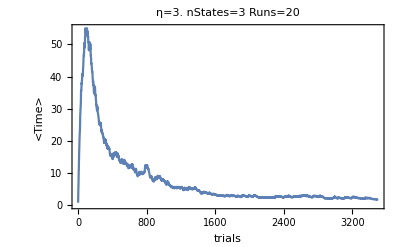

```mathematica
PlotnTimeInFile[iter,η,"Navig1n_Orig"]
```

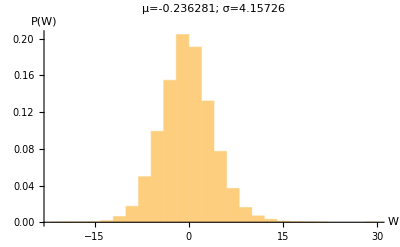

```mathematica
PlotWeightsInFile[iter,η,"Navig1n_Orig"]
```

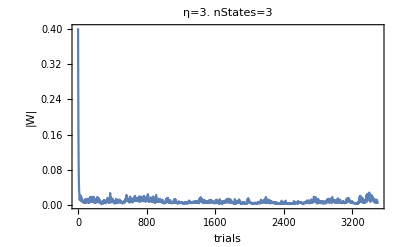

```mathematica
PlotWEvolInFile[iter,η,"Navig1n_Orig",0.2]
```

### Plot Best Perf

```mathematica
aAMPA=Round[N[0.2/Sqrt[nbNeuron*pConnect]],0.00000001];
σW=4.1;(* c(Z)~52% and N(Z)~1.05 activity *)
```

```mathematica
ColorsBar=Map[Directive[#,Opacity[0.4]]&,{Blue,Red,Darker@Green,Black ,Cyan,Purple,Brown}];
```

```mathematica
{statNMDASp,SpikeTimes,FirstSpikeTimes,VolMembs}=GetFinalStatFromFile[NavFName];FirstSpikeTimes=Map[Flatten[#] step &,FirstSpikeTimes];SpikeTimes=Map[Flatten[#] step &,SpikeTimes];
```

```mathematica
rip[graphics_, {xl_, xh_}, {yl_, yh_}] := Block[ {t, is, pr},
  t = ImportString[ExportString[graphics, "EPS"], "EPS"];
  is = ImageSize /. Cases[t, HoldPattern[ImageSize -> _], Infinity];
  pr = is {{xl, xh}, {yl, yh}};
  is = is {xh - xl, yh - yl};
  t /. (PlotRange -> _) -> (PlotRange -> 
       pr) /. (ImageSize -> _) -> (ImageSize -> is) 
  ]
```

```mathematica
PlotSpTimeFin=GraphicsColumn[
 {rip[PlotSpTime, {0, 1}, {0.85,1}],
  rip[PlotSpTime, {0, 1}, {0,0.35}]},Left,-10]
```

-Graphics-

```mathematica
Export["PlotSpTimeNavig.png",PlotSpTimeFin]
```

PlotSpTimeNavig.png

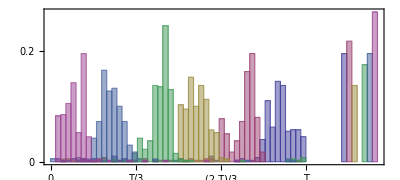

```mathematica
PlotSpTime=Histogram[Drop[FirstSpikeTimes,{nStates+1,nStates+1}],{10},"Probability",(*FrameLabel->{"Perf (%)","P(Perf)"},*)BaseStyle->{22,Thickness[0.01]},LabelStyle->(FontFamily->"Helvetica"),(*ChartStyle->{Darker@Green,Blue,Red},*)Axes->False,ImageSize->400,Frame->{{False,False},{True,False}},FrameTicks->{{{0,0.2,0.4},None},{{{0,
0},{500/6,"T/6"},{2 500/6,"T/3"},{3 500/6,"T/2"},{4 500/6,"(2  T)/3"},{5 500/6,"(5  T)/6"},{500,"T"},{PosEmpSptTrain+5*Patn,"∅"}},None}},ImageSize->400,PlotRange->All,PlotRangePadding->{{0,-120},{0.,0.01}},ImagePadding->{{39,30},{40,0}},AspectRatio->0.45]
```

```mathematica
Export["PlotSpTimeNavig.eps",PlotSpTime]
```

PlotSpTimeNavig.eps

```mathematica
Export["PlotSpTimeNavig.png",PlotSpTime]
```

PlotSpTimeNavig.png

```mathematica
SpTstate0=FirstSpikeTimes[[nStates+1]];
```

```mathematica
Length@Select[SpTstate0,#>500&]/Length@SpTstate0//N
```

0.91

```mathematica
mGamesIni=getMeanGameLenIni[NavFName]
```

{18.5714,6.5436}

```mathematica
mGamesIni={18.571428571428573,6.543602791368837};
```

```mathematica
rest=ReadList[NavFName];
```

```mathematica
PerfGlob=rest/.trialDT[outDT[a_],_,_,_,_]->a;;
```

```mathematica
PerfGlob=Map[λFilter[#,0.2/Patn,mGamesIni[[1]]]&,PerfGlob];
```

```mathematica
iter=500*Patn;
```

```mathematica
DeltaTrial=Round[iter/10]
```

350

```mathematica
GlobRange=Range[1+DeltaTrial,iter,DeltaTrial]~Join~{iter};
```

```mathematica
ErrorPtsGlob={{{1,mGamesIni[[1]]},ErrorBar[mGamesIni[[2]]]}}~Join~MapThread[{{#3,#1},ErrorBar[#2]}&,{(Mean@PerfGlob)[[GlobRange]],(StandardDeviation@PerfGlob/Sqrt[Length@PerfGlob-1])[[GlobRange]],GlobRange}];
```

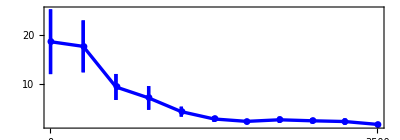

```mathematica
PlotmGamesNavig=
ErrorListPlot[ErrorPtsGlob,Joined->True,Frame->True,Axes->False,ImageSize->400,FrameTicks->{{{10,20},None},{{0,iter},None}},BaseStyle->22,LabelStyle->(FontFamily->"Helvetica"),(*FrameLabel->{"trials","Performance (%)"},*)PlotRange->All,PlotStyle->{{Blue,Thickness[0.006]},{Darker@Green,Thickness[0.006]}},PlotMarkers->Automatic,ImagePadding->{{39,30},{40,0}},AspectRatio->0.35]
```

```mathematica
Export["PlotmGamesNavig.png",PlotmGamesNavig]
```

PlotmGamesNavig.png

```mathematica
Export["PlotmGamesNavig.png",-Graphics-,ImageResolution->600]
```

PlotmGamesNavig.png

#### dataSp Time

```mathematica
FirstSpikeTimes
```

FirstSpikeTimes

```mathematica
dataFirstSpikeTimes={{570.,570.,570.,438.40000000000003,570.,570.,570.,570.,570.,570.,124.2,438.40000000000003,570.,471.6,444.40000000000003,570.,570.,570.,570.,570.,570.,570.,570.,570.,570.,570.,461.40000000000003,486.20000000000005,570.,570.,496.40000000000003,570.,493.20000000000005,570.,488.20000000000005,76.4,486.40000000000003,570.,265.2,570.,450.8,449.20000000000005,570.,450.40000000000003,450.8,451.40000000000003,449.20000000000005,443.40000000000003,458.,450.8,451.20000000000005,450.8,464.8,457.,448.,450.40000000000003,448.8,450.,449.8,44.,429.40000000000003,429.8,419.8,430.40000000000003,419.40000000000003,424.,419.,429.8,422.40000000000003,421.8,134.8,421.20000000000005,431.,433.,430.20000000000005,430.20000000000005,432.8,144.4,428.20000000000005,430.20000000000005,438.,460.8,444.40000000000003,570.,440.8,435.,438.40000000000003,128.4,440.6,438.8,438.,443.20000000000005,439.40000000000003,440.40000000000003,445.8,437.,442.40000000000003,446.20000000000005,438.8,439.20000000000005,450.40000000000003,447.,451.8,450.,463.6,570.,570.,454.20000000000005,407.40000000000003,447.6,461.,458.8,462.40000000000003,453.,454.6,460.8,445.6,570.,447.8,570.,129.8,314.,423.20000000000005,418.8,422.20000000000005,570.,420.40000000000003,421.,422.,425.8,420.,421.20000000000005,420.,419.8,422.,316.8,422.40000000000003,431.8,421.20000000000005,425.20000000000005,570.,489.6,570.,495.20000000000005,493.40000000000003,486.6,488.40000000000003,496.,494.,570.,491.6,493.,12.600000000000001,570.,493.8,570.,488.40000000000003,453.,494.,497.8,570.,570.,476.6,486.20000000000005,467.8,489.,570.,570.,469.20000000000005,449.8,486.8,435.6,570.,478.,416.,570.,480.6,464.8,13.8,426.20000000000005,410.,425.20000000000005,424.8,315.8,412.6,570.,424.20000000000005,418.8,424.6,429.20000000000005,570.,426.40000000000003,409.6,182.8,570.,428.,452.8,424.,424.,409.8,445.6,444.8,444.6,570.,444.6,446.,376.8,444.40000000000003,443.40000000000003,444.20000000000005,444.20000000000005,445.20000000000005,444.40000000000003,446.,570.,445.,377.40000000000003,444.,445.6,447.6,485.8,570.,85.2,64.,570.,255.4,81.,452.6,570.,455.20000000000005,482.20000000000005,570.,455.,458.8,449.,480.40000000000003,468.8,448.8,453.6,456.8,457.8,317.,458.40000000000003,460.8,456.8,458.20000000000005,457.40000000000003,457.6,458.20000000000005,458.20000000000005,458.6,457.6,459.6,463.6,391.6,45.2,459.40000000000003,458.40000000000003,463.8,457.6,420.,418.40000000000003,420.,424.8,172.60000000000002,422.40000000000003,419.8,419.8,419.20000000000005,68.4,420.40000000000003,421.,419.40000000000003,421.,420.8,419.20000000000005,29.,419.6,420.20000000000005,422.20000000000005,570.,570.,570.,444.20000000000005,485.8,570.,440.6,570.,439.20000000000005,439.40000000000003,121.4,570.,570.,570.,570.,570.,446.6,442.6,441.6,439.,461.,253.8,458.,458.6,420.8,469.40000000000003,243.8,431.8,427.,454.20000000000005,461.40000000000003,433.8,570.,457.6,428.,459.40000000000003,170.8,570.,452.,458.20000000000005,450.6,449.6,449.40000000000003,450.,452.20000000000005,449.,448.40000000000003,448.6,449.8,448.8,448.,447.8,451.6,449.6,447.40000000000003,451.40000000000003,450.40000000000003,456.8,449.20000000000005,448.6,570.,570.,570.,445.20000000000005,477.20000000000005,570.,570.,153.,570.,467.40000000000003,473.8,460.6,483.6,570.,478.8,204.4,473.6,469.20000000000005,459.40000000000003,147.4,470.8,471.6,471.40000000000003,473.20000000000005,472.20000000000005,570.,469.6,472.8,474.40000000000003,477.,474.6,475.6,570.,327.20000000000005,476.8,570.,474.8,475.20000000000005,475.20000000000005,474.,482.20000000000005,498.,465.8,570.,489.8,490.8,493.8,487.,480.40000000000003,570.,479.,447.8,487.8,368.,495.20000000000005,490.6,490.,489.6,485.40000000000003,491.},{336.8,336.,335.40000000000003,337.6,334.8,374.20000000000005,335.6,335.20000000000005,335.,336.8,335.40000000000003,336.8,336.40000000000003,339.,335.40000000000003,336.,339.8,335.6,337.6,337.,396.,580.,580.,580.,400.40000000000003,580.,580.,580.,405.8,396.8,580.,398.,398.8,580.,580.,399.6,580.,580.,396.8,580.,388.40000000000003,386.40000000000003,387.20000000000005,384.20000000000005,384.6,385.,395.6,580.,385.40000000000003,394.40000000000003,387.,385.20000000000005,381.6,387.,381.6,391.20000000000005,385.40000000000003,380.8,385.40000000000003,384.,405.6,409.8,409.,131.8,408.20000000000005,57.6,86.,410.,101.4,411.20000000000005,101.80000000000001,408.,63.400000000000006,407.8,407.,409.,410.6,411.20000000000005,405.20000000000005,408.8,385.6,390.8,388.,361.6,391.,391.20000000000005,390.20000000000005,390.20000000000005,390.,391.40000000000003,298.,390.8,387.8,286.8,390.,389.8,387.6,390.40000000000003,365.8,389.6,353.,399.,372.40000000000003,367.20000000000005,366.,374.8,580.,71.8,373.40000000000003,367.,580.,580.,389.8,354.40000000000003,367.8,580.,368.40000000000003,365.6,365.40000000000003,580.,344.40000000000003,339.6,340.8,340.20000000000005,341.20000000000005,337.40000000000003,340.8,340.20000000000005,343.20000000000005,339.20000000000005,339.20000000000005,340.20000000000005,338.8,338.6,102.80000000000001,340.,340.6,339.8,340.20000000000005,339.,385.6,385.6,385.20000000000005,393.8,390.8,391.20000000000005,376.8,391.6,387.,389.6,389.40000000000003,390.,389.20000000000005,318.,393.40000000000003,387.6,389.20000000000005,389.20000000000005,390.,388.8,389.6,580.,92.2,371.40000000000003,580.,580.,402.,370.40000000000003,311.8,400.20000000000005,580.,580.,392.,390.,580.,389.,580.,362.40000000000003,394.8,389.6,377.,377.20000000000005,306.6,375.,374.20000000000005,238.4,373.6,375.20000000000005,381.20000000000005,335.20000000000005,383.40000000000003,373.20000000000005,580.,375.6,375.6,372.,580.,374.8,363.6,367.40000000000003,334.6,161.8,353.8,354.40000000000003,352.,348.40000000000003,348.6,187.20000000000002,345.40000000000003,351.,349.20000000000005,345.40000000000003,349.,307.20000000000005,348.8,336.6,181.60000000000002,345.40000000000003,335.40000000000003,349.8,127.2,388.40000000000003,391.20000000000005,388.,580.,395.8,387.40000000000003,356.20000000000005,361.20000000000005,410.40000000000003,394.20000000000005,392.40000000000003,580.,580.,580.,580.,580.,580.,487.8,383.40000000000003,409.,580.,580.,580.,580.,580.,410.,580.,580.,580.,580.,408.,580.,580.,408.6,580.,580.,580.,580.,408.20000000000005,390.8,388.,389.,384.40000000000003,390.6,390.6,390.20000000000005,390.20000000000005,390.40000000000003,391.,389.8,389.40000000000003,388.40000000000003,390.20000000000005,390.6,389.8,390.6,390.20000000000005,390.6,392.6,580.,580.,580.,580.,580.,117.80000000000001,580.,580.,580.,29.,580.,580.,580.,580.,580.,580.,580.,580.,580.,580.,380.,386.40000000000003,385.,378.20000000000005,373.6,391.40000000000003,381.6,385.40000000000003,373.8,382.8,381.6,385.6,384.6,390.6,384.8,371.6,386.,399.,374.40000000000003,386.,396.40000000000003,396.20000000000005,398.40000000000003,396.40000000000003,395.6,396.8,394.,396.8,398.,396.40000000000003,395.8,220.,398.8,395.,397.6,395.40000000000003,396.40000000000003,396.20000000000005,397.8,395.8,408.6,580.,403.8,403.6,580.,395.20000000000005,394.20000000000005,265.40000000000003,393.40000000000003,392.8,580.,391.40000000000003,580.,580.,387.8,405.,270.6,398.40000000000003,407.8,276.6,580.,580.,580.,580.,408.8,407.20000000000005,406.6,62.6,408.,406.,580.,405.6,413.6,580.,580.,404.40000000000003,407.,404.6,580.,580.,377.20000000000005,580.,392.8,378.40000000000003,393.40000000000003,381.20000000000005,580.,219.60000000000002,378.6,379.6,580.,580.,361.8,580.,377.40000000000003,380.,361.8,580.,393.20000000000005,377.6},{290.2,287.2,278.,284.8,280.40000000000003,283.,590.,590.,280.2,279.2,280.6,590.,100.,286.8,305.6,590.,280.8,283.2,288.,302.,301.,294.,294.2,293.6,297.2,294.,286.2,286.8,295.2,288.2,290.40000000000003,287.6,296.2,295.2,288.,294.6,295.,295.8,293.2,293.8,590.,590.,590.,590.,590.,590.,590.,590.,590.,590.,282.,590.,590.,325.20000000000005,590.,590.,590.,590.,590.,590.,299.40000000000003,330.6,590.,295.,306.8,311.6,305.40000000000003,590.,590.,590.,299.2,590.,295.40000000000003,277.40000000000003,590.,590.,292.8,297.6,304.,590.,276.40000000000003,323.40000000000003,288.2,321.20000000000005,303.8,290.8,321.8,590.,321.,282.6,324.,319.40000000000003,107.2,313.40000000000003,321.20000000000005,323.,322.,320.8,328.8,309.,339.6,590.,590.,590.,297.8,343.20000000000005,317.,297.6,590.,311.40000000000003,300.40000000000003,295.40000000000003,312.6,590.,345.8,27.400000000000002,590.,590.,297.,590.,277.,279.40000000000003,307.,277.2,286.8,279.,277.,304.40000000000003,271.40000000000003,277.2,318.6,278.,287.6,277.6,278.,278.,281.40000000000003,285.2,278.6,285.6,262.,265.6,263.2,263.8,261.8,263.6,259.40000000000003,265.6,267.8,88.60000000000001,264.2,263.2,270.,265.2,266.8,262.40000000000003,268.40000000000003,90.4,263.2,261.40000000000003,281.,590.,288.,295.8,293.40000000000003,299.,301.,279.40000000000003,162.20000000000002,281.6,279.8,267.40000000000003,290.,281.6,288.,283.2,590.,304.2,296.2,280.8,296.6,590.,298.6,298.6,293.6,297.8,299.6,278.6,296.40000000000003,297.6,208.,152.20000000000002,304.,296.2,281.,297.40000000000003,297.8,298.6,299.8,269.,272.6,128.20000000000002,274.40000000000003,274.40000000000003,273.8,274.8,271.6,275.,275.6,275.40000000000003,275.40000000000003,273.6,274.40000000000003,274.6,278.,275.8,276.2,277.40000000000003,273.6,278.,274.8,590.,267.6,590.,263.8,590.,263.,39.6,590.,257.2,259.6,104.,261.6,590.,260.40000000000003,264.,28.8,92.2,264.40000000000003,590.,590.,299.6,304.6,336.,306.2,302.,299.8,274.40000000000003,297.,300.40000000000003,302.8,305.2,302.8,302.,302.2,304.6,300.2,301.8,303.2,307.40000000000003,276.40000000000003,286.,287.6,290.40000000000003,590.,270.6,285.2,287.,590.,291.40000000000003,275.2,271.2,590.,288.6,293.8,292.6,287.6,274.8,264.,148.4,305.6,307.6,317.,315.6,313.,314.40000000000003,273.8,313.8,269.8,590.,279.,281.,590.,275.2,298.8,590.,270.40000000000003,273.6,311.,313.,307.,295.40000000000003,300.8,309.,313.40000000000003,286.40000000000003,303.,296.40000000000003,302.40000000000003,307.40000000000003,301.,300.,302.6,301.40000000000003,296.,285.8,301.40000000000003,306.2,310.8,302.6,255.20000000000002,254.20000000000002,254.20000000000002,253.20000000000002,254.8,253.8,253.20000000000002,254.,254.4,253.60000000000002,253.20000000000002,254.,254.20000000000002,253.4,254.60000000000002,254.8,253.8,255.,253.60000000000002,253.60000000000002,307.6,327.6,321.,322.8,322.,310.20000000000005,311.20000000000005,327.6,319.40000000000003,306.40000000000003,319.8,321.40000000000003,329.20000000000005,313.20000000000005,321.6,36.,327.40000000000003,320.8,318.20000000000005,313.40000000000003,257.,259.40000000000003,255.20000000000002,253.60000000000002,253.20000000000002,253.60000000000002,253.8,253.8,253.8,255.,254.,252.8,253.60000000000002,252.,253.20000000000002,257.6,261.40000000000003,254.,263.,252.60000000000002,275.,266.8,264.8,269.6,269.40000000000003,270.8,276.,275.8,273.2,274.2,270.,271.6,272.,268.6,268.40000000000003,267.40000000000003,272.2,48.2,269.2,268.8},{600.,600.,600.,600.,600.,600.,600.,600.,600.,600.,600.,600.,497.8,600.,600.,600.,391.40000000000003,600.,600.,600.,600.,600.,600.,600.,600.,600.,600.,600.,600.,600.,148.20000000000002,600.,600.,600.,600.,600.,600.,600.,600.,600.,600.,600.,600.,600.,600.,600.,600.,600.,600.,600.,600.,600.,600.,600.,600.,600.,600.,600.,600.,600.,600.,600.,188.60000000000002,600.,600.,180.20000000000002,600.,600.,600.,600.,165.4,469.,600.,600.,600.,600.,600.,600.,470.,600.,600.,600.,600.,600.,600.,600.,218.8,175.8,600.,183.4,600.,600.,229.60000000000002,600.,600.,600.,600.,600.,600.,600.,600.,600.,600.,600.,600.,600.,600.,600.,600.,600.,600.,600.,600.,600.,600.,600.,600.,600.,600.,600.,600.,600.,600.,600.,271.6,600.,600.,600.,600.,600.,600.,600.,600.,600.,600.,600.,600.,600.,600.,600.,600.,600.,600.,600.,600.,600.,600.,600.,600.,600.,600.,143.,600.,600.,600.,600.,600.,600.,600.,600.,600.,600.,600.,600.,600.,600.,600.,600.,600.,600.,73.4,600.,600.,600.,37.,600.,600.,600.,600.,600.,600.,600.,600.,600.,600.,600.,600.,600.,600.,60.6,600.,600.,600.,600.,422.40000000000003,600.,600.,341.8,600.,600.,600.,47.2,600.,220.,600.,600.,600.,600.,600.,67.8,600.,600.,600.,600.,600.,600.,600.,334.,600.,600.,600.,600.,600.,600.,600.,600.,600.,600.,600.,600.,600.,600.,600.,600.,600.,600.,600.,600.,600.,600.,600.,600.,600.,600.,600.,600.,110.4,600.,600.,600.,600.,600.,600.,600.,600.,600.,600.,462.,600.,600.,600.,600.,600.,600.,600.,600.,600.,89.60000000000001,600.,600.,600.,600.,600.,600.,600.,403.,600.,600.,600.,600.,600.,600.,600.,600.,600.,600.,600.,600.,600.,600.,600.,600.,600.,600.,600.,600.,600.,600.,600.,600.,600.,402.6,600.,600.,600.,116.80000000000001,600.,600.,600.,600.,600.,410.,600.,600.,600.,600.,600.,600.,600.,600.,600.,600.,600.,600.,600.,600.,600.,368.8,600.,600.,93.60000000000001,600.,600.,600.,600.,600.,600.,600.,600.,600.,600.,600.,600.,600.,600.,600.,600.,600.,600.,600.,600.,600.,600.,600.,600.,600.,600.,600.,600.,600.,600.,281.8,600.,463.8,600.,600.,600.,600.,600.,600.,600.,600.,600.,600.,600.,600.,600.,600.,600.,600.,600.,600.,600.,600.,600.,600.,600.,600.,600.,600.,600.,600.,600.,600.,600.,187.4,600.,30.,600.,600.},{229.4,238.4,211.20000000000002,226.8,224.4,144.8,205.8,227.8,229.60000000000002,226.,277.2,229.8,227.4,202.4,227.8,200.,234.60000000000002,610.,610.,232.20000000000002,229.8,241.4,226.60000000000002,224.,238.20000000000002,241.20000000000002,222.8,228.4,228.4,610.,105.,234.4,610.,610.,228.60000000000002,238.8,227.,610.,125.4,229.20000000000002,234.60000000000002,236.8,234.8,610.,239.20000000000002,610.,236.20000000000002,224.60000000000002,234.8,229.60000000000002,234.4,235.20000000000002,212.4,235.8,235.4,223.60000000000002,234.8,235.4,236.4,236.60000000000002,610.,187.20000000000002,179.60000000000002,610.,189.8,167.8,170.,168.,185.60000000000002,610.,170.8,610.,172.,170.20000000000002,170.8,169.,173.60000000000002,168.8,169.4,168.8,207.4,129.,201.8,205.60000000000002,203.20000000000002,203.4,202.8,204.20000000000002,193.60000000000002,206.60000000000002,200.4,201.8,186.60000000000002,211.20000000000002,200.8,207.60000000000002,370.40000000000003,201.60000000000002,202.60000000000002,206.60000000000002,610.,220.20000000000002,220.8,218.8,220.60000000000002,220.,221.,610.,220.20000000000002,220.,221.60000000000002,218.60000000000002,222.4,219.8,221.8,222.,221.,224.20000000000002,219.4,220.,216.4,211.60000000000002,209.20000000000002,208.4,209.8,210.,209.60000000000002,209.4,210.,210.,209.60000000000002,208.4,209.,210.,210.8,210.,610.,209.8,208.4,210.20000000000002,214.60000000000002,214.4,212.20000000000002,610.,214.20000000000002,221.,217.20000000000002,215.8,215.4,610.,214.8,217.,223.60000000000002,214.4,218.4,213.60000000000002,217.,214.8,213.8,219.4,225.20000000000002,194.8,215.20000000000002,226.20000000000002,239.20000000000002,222.,232.8,183.20000000000002,238.4,227.20000000000002,228.60000000000002,225.,226.,150.,229.20000000000002,235.,221.4,220.60000000000002,237.60000000000002,245.20000000000002,233.4,235.4,235.4,234.60000000000002,234.4,234.60000000000002,234.8,233.8,234.60000000000002,233.8,236.,236.4,234.20000000000002,232.60000000000002,235.,230.4,234.20000000000002,233.20000000000002,235.,241.4,209.,206.,207.60000000000002,222.4,211.8,198.20000000000002,210.8,610.,219.4,207.8,210.20000000000002,195.60000000000002,207.4,195.8,218.4,207.60000000000002,190.4,205.,221.20000000000002,218.,207.4,204.20000000000002,204.4,208.,204.,206.,206.8,211.20000000000002,173.20000000000002,50.800000000000004,204.60000000000002,205.60000000000002,208.,205.60000000000002,205.,210.20000000000002,208.20000000000002,204.60000000000002,205.8,206.60000000000002,224.60000000000002,228.8,232.8,223.8,228.8,224.4,229.4,222.60000000000002,218.60000000000002,222.,222.4,224.4,223.,227.60000000000002,198.60000000000002,229.8,224.8,229.20000000000002,231.,220.,172.20000000000002,170.8,173.4,224.60000000000002,171.60000000000002,172.8,226.60000000000002,610.,171.8,175.,175.8,232.4,225.20000000000002,224.4,230.20000000000002,171.,204.20000000000002,610.,467.,224.60000000000002,232.4,227.,253.20000000000002,224.8,226.8,230.60000000000002,610.,226.60000000000002,228.8,610.,610.,610.,610.,244.60000000000002,224.20000000000002,610.,225.,610.,610.,232.4,610.,610.,610.,610.,610.,610.,610.,610.,610.,610.,610.,610.,610.,610.,610.,610.,610.,610.,246.,236.8,224.4,223.,222.8,224.,224.20000000000002,224.20000000000002,225.20000000000002,224.,217.20000000000002,223.60000000000002,223.4,223.,224.8,216.20000000000002,223.8,222.8,224.,223.8,225.,223.,208.60000000000002,207.4,212.4,610.,218.,214.,211.8,610.,610.,180.20000000000002,610.,222.,211.8,212.,261.8,211.8,224.4,214.,211.4,218.8,188.8,198.,610.,610.,610.,198.60000000000002,195.60000000000002,188.20000000000002,610.,610.,193.,195.20000000000002,190.20000000000002,610.,188.4,610.,202.60000000000002,197.60000000000002,222.8,190.,610.,610.,472.40000000000003,610.,478.20000000000005,610.,496.40000000000003,610.,491.6,610.,610.,259.8,610.,610.,610.,483.20000000000005,610.,610.,494.8,610.},{120.2,119.2,140.20000000000002,9.,22.400000000000002,143.20000000000002,146.20000000000002,65.2,116.80000000000001,140.4,142.4,122.80000000000001,125.60000000000001,117.4,117.60000000000001,138.,160.60000000000002,149.8,149.20000000000002,88.,620.,620.,99.4,100.60000000000001,620.,620.,101.4,99.2,137.6,86.60000000000001,620.,133.20000000000002,97.2,620.,386.20000000000005,620.,620.,620.,101.2,98.60000000000001,103.2,110.60000000000001,620.,105.80000000000001,98.2,84.,620.,109.4,102.80000000000001,111.80000000000001,102.80000000000001,98.2,95.2,620.,110.,109.4,109.2,105.2,99.80000000000001,99.,620.,124.60000000000001,125.,73.8,125.,126.2,125.2,122.60000000000001,620.,124.80000000000001,126.,72.60000000000001,124.4,122.80000000000001,124.4,124.,124.4,124.4,126.80000000000001,128.20000000000002,105.4,109.4,105.80000000000001,101.60000000000001,152.20000000000002,138.20000000000002,100.,103.2,96.,101.2,105.80000000000001,104.4,136.4,620.,104.,96.80000000000001,102.60000000000001,96.4,103.,620.,112.2,107.60000000000001,111.60000000000001,112.80000000000001,116.,110.4,108.2,620.,112.2,111.80000000000001,109.80000000000001,113.,111.4,7.4,115.60000000000001,111.80000000000001,110.,112.,110.60000000000001,620.,120.4,86.80000000000001,102.60000000000001,100.2,102.80000000000001,120.80000000000001,100.4,100.4,89.60000000000001,117.80000000000001,118.4,98.4,121.80000000000001,96.4,118.2,117.60000000000001,92.2,91.60000000000001,92.60000000000001,103.80000000000001,620.,91.60000000000001,93.2,93.,90.4,620.,620.,620.,620.,89.80000000000001,468.20000000000005,85.60000000000001,101.80000000000001,620.,620.,620.,620.,620.,620.,620.,139.4,90.60000000000001,137.20000000000002,86.2,111.80000000000001,89.,205.4,147.6,143.,137.6,140.6,133.8,159.8,146.6,135.8,146.20000000000002,137.4,138.6,85.80000000000001,140.20000000000002,145.20000000000002,150.8,115.2,128.8,89.4,92.80000000000001,369.40000000000003,148.20000000000002,117.60000000000001,127.4,126.4,125.4,157.4,90.4,128.6,105.60000000000001,122.60000000000001,620.,125.2,111.60000000000001,133.20000000000002,130.6,132.4,142.8,137.8,140.6,140.,142.4,150.8,141.20000000000002,141.20000000000002,138.20000000000002,133.20000000000002,139.8,138.6,140.8,139.6,133.6,132.4,141.20000000000002,125.4,126.,620.,129.8,130.,134.20000000000002,121.60000000000001,125.,122.4,140.4,121.,620.,123.80000000000001,121.80000000000001,126.60000000000001,124.80000000000001,120.60000000000001,142.20000000000002,158.20000000000002,137.8,620.,136.6,54.,164.20000000000002,620.,204.4,469.8,477.40000000000003,620.,620.,620.,169.20000000000002,620.,620.,149.,154.4,620.,620.,620.,620.,620.,162.,154.60000000000002,120.4,125.2,109.4,122.,113.80000000000001,620.,163.60000000000002,162.,620.,620.,150.20000000000002,144.6,620.,144.20000000000002,163.60000000000002,125.60000000000001,158.8,98.2,620.,118.80000000000001,620.,620.,620.,620.,120.60000000000001,620.,116.2,620.,113.4,130.8,620.,115.4,620.,620.,133.4,620.,620.,108.60000000000001,109.80000000000001,106.4,106.80000000000001,108.,107.2,107.60000000000001,620.,106.60000000000001,115.,107.4,620.,109.2,107.,106.4,106.80000000000001,112.,109.4,56.6,108.,110.80000000000001,110.4,112.60000000000001,80.2,109.2,118.4,103.2,109.80000000000001,110.2,112.2,106.,109.60000000000001,118.4,116.60000000000001,104.2,113.,105.2,620.,110.4,104.,148.4,135.20000000000002,135.,125.4,54.400000000000006,158.4,620.,132.20000000000002,63.400000000000006,122.2,151.20000000000002,134.,134.4,136.,33.2,131.4,620.,135.6,126.4,138.20000000000002,620.,89.2,620.,83.80000000000001,620.,620.,620.,620.,89.4,620.,620.,620.,84.60000000000001,620.,84.2,620.,93.,91.2,620.,113.60000000000001,117.,108.2,124.4,117.80000000000001,136.6,104.4,124.80000000000001,108.4,90.80000000000001,108.4,99.60000000000001,125.,108.80000000000001,103.80000000000001,117.80000000000001,124.4,113.2,131.,107.80000000000001,105.4},{68.8,72.4,63.,630.,68.4,71.2,61.800000000000004,71.,72.2,62.,76.,55.,630.,630.,67.2,76.4,61.400000000000006,68.2,65.2,91.2,630.,630.,630.,630.,630.,630.,630.,630.,630.,630.,630.,630.,630.,630.,630.,630.,630.,364.20000000000005,630.,630.,69.,67.8,68.,225.8,65.4,630.,69.,68.,61.400000000000006,66.60000000000001,75.,64.8,183.8,61.2,66.,63.6,630.,69.8,74.2,72.2,66.2,66.2,65.2,65.4,67.,65.60000000000001,65.60000000000001,70.,67.8,70.60000000000001,65.8,65.,65.4,66.2,67.,66.2,66.,65.8,66.2,65.,45.,54.400000000000006,45.6,48.,630.,630.,111.80000000000001,45.,32.4,48.400000000000006,47.800000000000004,50.400000000000006,49.400000000000006,30.8,45.400000000000006,49.,630.,46.400000000000006,36.6,46.,630.,630.,39.400000000000006,33.,33.800000000000004,49.,630.,630.,14.8,17.6,13.8,12.600000000000001,45.,630.,630.,303.8,630.,630.,15.4,630.,46.,34.6,630.,37.800000000000004,40.800000000000004,39.400000000000006,43.400000000000006,63.,47.2,40.400000000000006,41.6,42.400000000000006,630.,630.,43.,41.2,34.4,40.,630.,40.,40.6,630.,23.400000000000002,630.,153.60000000000002,66.60000000000001,62.,66.2,14.,47.2,60.400000000000006,43.2,57.800000000000004,22.8,45.400000000000006,60.400000000000006,63.6,62.6,630.,61.800000000000004,42.800000000000004,54.400000000000006,59.2,66.4,61.6,58.400000000000006,630.,59.800000000000004,66.2,630.,61.6,630.,64.2,61.6,61.,55.,630.,630.,56.,59.400000000000006,36.6,32.6,34.6,38.,31.200000000000003,33.,32.800000000000004,34.2,32.800000000000004,31.8,31.6,37.,30.6,32.6,34.,35.4,32.2,34.6,33.4,630.,65.60000000000001,53.6,20.200000000000003,29.200000000000003,57.800000000000004,47.800000000000004,30.8,47.,17.2,38.2,44.800000000000004,46.6,20.200000000000003,18.6,33.800000000000004,68.2,51.400000000000006,64.8,45.,48.,62.800000000000004,65.8,73.,67.2,62.6,63.800000000000004,63.400000000000006,70.,64.,65.2,62.6,62.800000000000004,78.60000000000001,66.8,64.,68.4,63.400000000000006,61.400000000000006,45.400000000000006,54.,26.,23.8,22.200000000000003,27.,22.200000000000003,30.200000000000003,22.200000000000003,27.,26.400000000000002,23.6,24.200000000000003,24.400000000000002,24.6,630.,26.6,36.800000000000004,29.6,630.,47.6,630.,17.,16.8,18.8,18.6,20.,18.,14.600000000000001,18.400000000000002,17.8,16.8,17.6,17.400000000000002,17.2,18.,16.8,16.2,18.,17.400000000000002,17.8,17.8,66.2,70.2,54.2,64.4,55.6,42.800000000000004,40.800000000000004,630.,41.2,55.400000000000006,44.400000000000006,630.,45.,49.6,40.,56.400000000000006,45.2,630.,12.4,43.800000000000004,19.,20.,19.200000000000003,23.200000000000003,24.200000000000003,30.,20.,22.8,24.200000000000003,23.200000000000003,21.200000000000003,20.400000000000002,21.6,20.400000000000002,29.200000000000003,23.8,24.400000000000002,18.400000000000002,13.600000000000001,19.8,630.,630.,630.,630.,630.,630.,95.4,630.,72.60000000000001,630.,77.4,630.,630.,630.,630.,630.,630.,630.,630.,630.,46.800000000000004,39.400000000000006,42.,33.800000000000004,45.400000000000006,42.,33.4,43.,77.2,32.,45.2,44.,39.,41.800000000000004,40.2,41.400000000000006,50.,46.800000000000004,36.,34.6,630.,630.,68.60000000000001,630.,630.,82.4,630.,68.8,58.800000000000004,630.,630.,630.,630.,630.,630.,630.,630.,630.,630.,630.,630.,630.,630.,630.,630.,630.,630.,630.,630.,630.,630.,630.,630.,630.,630.,630.,630.,630.,630.,630.}};
```

```mathematica
FirstSpikeTimes=dataFirstSpikeTimes;
```

### Plot spikes distribution after learning

```mathematica
NavFName=getFileName[3.,iter,"Navig1n_Orig"];
```

```mathematica
OptPadding={{30,15},{28,0}};
```

```mathematica
GetIniStatFromFileFast[nameFile_]:=Block[{tmp,res,spikeDiff,meanNbNMDASpikeTab={},resY,resZ,WTab,Seedtab,last,Y,Z,nbSample=20,tmp1,tmp2,indexTab,Wini,p},
res=ReadList[nameFile];
WTab=res/.trialDT[_,_,_,outDT[a_],_]->a;
Seedtab=res/.trialDT[_,_,_,_,outDT[a_]]->a;
res=Transpose@Table[
SeedRandom[Seedtab[[k]]];
{Wini,Mask} = myiniws[0,σW,nbNeuron,pConnect];
MakePats[];
Clear[Patsepsps];
Patsepsps[n_]:=Patsepsps[n]=Patsepsps0[n];
(*msg[WTab[[k]]];*)
stepperlist=0;
tmp=Transpose@Table[
Transpose@Table[
p=StateToPatn[state];
{last,{Y,Z}}=nextpassEpisodeEval[Patsepsps[p],ini[(*tmp*)Wini]];
{GetNbNMDAForAP[Z,Y],
If[Length[Z]==0,{(PosEmpSptTrain+10*p)/step},Z],If[Length[Z]==0,{(PosEmpSptTrain+10*p)/step},{First@Z}],
1-Sign@Abs@CalcNewStates[step Z,state]
}
,{state,-nStates,nStates}]
,{nbSample}];
stepperlist=0;
{Map[N@myMean@Flatten[#]&,Transpose[tmp[[1]]]],
Map[Flatten[#]&,Transpose[tmp[[2]]]],
Map[Flatten[#]&,Transpose[tmp[[3]]]],
Flatten@tmp[[4]]}
,{k,Length@Seedtab}];
tmp=Map[step*Cases[Flatten[#],Except[0]]&,Transpose[res[[2]]]];
indexTab=Range[Length@tmp2];
{Transpose[res[[1]]],Transpose[res[[2]]],Transpose[res[[3]]],Flatten[res[[4]]]}
];
```

```mathematica
{statNMDASpIni,SpikeTimesIni,FirstSpikeTimesIni,PerfIni}=GetIniStatFromFileFast[NavFName];FirstSpikeTimesIni=Map[Flatten[#] step &,FirstSpikeTimesIni];SpikeTimesIni=Map[Flatten[#] step &,SpikeTimesIni];
```

```mathematica
μPerfIni=PerfIni//Mean//N
```

0.128571

```mathematica
σPerfIni=N@StandardDeviation@PerfIni/Sqrt[Length@PerfIni/20]
```

0.0282945

```mathematica
σPerfIni/Sqrt[Length@PerfIni/20(*nb Sample*)]
```

0.00239132

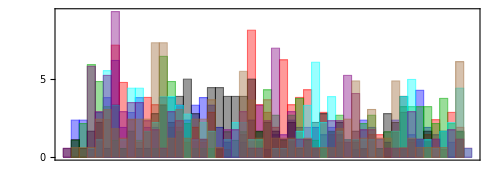

```mathematica
PlotSpTime=Histogram[Map[Function[t,Select[t,#<501&]],FirstSpikeTimesIni],{10},"Probability",(*FrameLabel->{"Perf (%)","P(Perf)"},*)BaseStyle->24,LabelStyle->(FontFamily->"Helvetica"),(*ChartStyle->{Darker@Green,Blue,Red},*)Axes->False,ImageSize->500,Frame->{{True,False},{True,False}},FrameTicks->{{{0,{0.05,5},{0.1,10}},None},{{{0,""},{500/6,""},{2 500/6,""},{3 500/6,""},{4 500/6,""},{5 500/6,""},{500/6,""},{500,""}},None}},ImageSize->500,PlotRange->All,PlotRangePadding->{{0,0},(*Automatic*){0.0,0.025}},
ImagePadding->{{39,35},{40,2}},
FrameTicksStyle->{{Black,Black},{{Black,Thickness[0.015]},Black}},
ChartStyle->ColorsBar,AspectRatio->0.35]
```

```mathematica
Export["PlotSpNavigTimePre.png",PlotSpTime,ImageResolution->600]
```

PlotSpNavigTimePre.png

```mathematica
GetFinalStatFromFileFast[nameFile_]:=Block[{tmp,res,spikeDiff,meanNbNMDASpikeTab={},resY,resZ,WTab,Seedtab,last,Y,Z,nbSample=20,tmp1,tmp2,indexTab,Wini,p},
res=ReadList[nameFile];
WTab=res/.trialDT[_,_,_,outDT[a_],_]->a;
Seedtab=res/.trialDT[_,_,_,_,outDT[a_]]->a;
res=Transpose@Table[
SeedRandom[Seedtab[[k]]];
{Wini,Mask} = myiniws[0,σW,nbNeuron,pConnect];
MakePats[];
Clear[Patsepsps];
Patsepsps[n_]:=Patsepsps[n]=Patsepsps0[n];
(*msg[WTab[[k]]];*)
stepperlist=0;
tmp=Transpose@Table[
Transpose@Table[
p=StateToPatn[state];
{last,{Y,Z}}=nextpassEpisodeEval[Patsepsps[p],ini[WTab[[k]]]];
{GetNbNMDAForAP[Z,Y],
If[Length[Z]==0,{(PosEmpSptTrain+10*p)/step},Z],If[Length[Z]==0,{(PosEmpSptTrain+10*p)/step},{First@Z}],
1-Sign@Abs@CalcNewStates[step Z,state]
}
,{state,-nStates,nStates}]
,{nbSample}];
stepperlist=0;
{Map[N@myMean@Flatten[#]&,Transpose[tmp[[1]]]],
Map[Flatten[#]&,Transpose[tmp[[2]]]],
Map[Flatten[#]&,Transpose[tmp[[3]]]],
Flatten@tmp[[4]]}
,{k,Length@Seedtab}];
tmp=Map[step*Cases[Flatten[#],Except[0]]&,Transpose[res[[2]]]];
indexTab=Range[Length@tmp2];
{Transpose[res[[1]]],Transpose[res[[2]]],Transpose[res[[3]]],Flatten[res[[4]]]}
];
```

```mathematica
{statNMDASp,SpikeTimes,FirstSpikeTimes,PerfFinal}=GetFinalStatFromFileFast[NavFName];FirstSpikeTimesIni=Map[Flatten[#] step &,FirstSpikeTimesIni];SpikeTimesIni=Map[Flatten[#] step &,SpikeTimesIni];
```

```mathematica
μPerfFinal=PerfFinal//Mean//N
```

0.768571

```mathematica
σPerfFinal=N@StandardDeviation@PerfFinal/Sqrt[Length@PerfFinal/20]
```

0.0356504

```mathematica
σPerfFinal/Sqrt[Length@PerfFinal/20(*nb Sample*)]
```

0.00301301

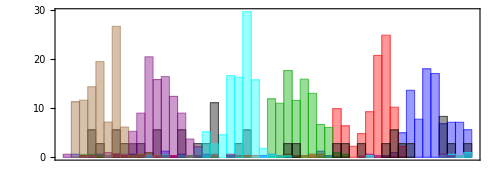

```mathematica
PlotSpTime=Histogram[Map[Function[t,Select[t,#<501&]],FirstSpikeTimes],{10},"Probability",(*FrameLabel->{"Perf (%)","P(Perf)"},*)BaseStyle->24,LabelStyle->(FontFamily->"Helvetica"),(*ChartStyle->{Darker@Green,Blue,Red},*)Axes->False,ImageSize->500,Frame->{{True,False},{True,False}},FrameTicks->{{{0,{0.1,10},{0.2,20},{0.3,30}},None},{{{0,""},{500/6,""},{2 500/6,""},{3 500/6,""},{4 500/6,""},{5 500/6,""},{500/6,""},{500,""}},None}},ImageSize->500,PlotRange->All,PlotRangePadding->{{0,0},(*Automatic*){0.0,0.025}},
ImagePadding->{{39,35},{40,2}},
FrameTicksStyle->{{Black,Black},{{Black,Thickness[0.015]},Black}},
ChartStyle->ColorsBar,AspectRatio->0.35]
```

```mathematica
Export["PlotSpNavigTimePost.png",PlotSpTime,ImageResolution->600]
```

PlotSpNavigTimePost.png